```mathematica
xn[a_,b_,g_,n_]:=(a 3^(n+1)+b 5^(n+1)+g 100^(n+1))/(a 3^n+b 5^n+g 100^n)
abg[x0_,x1_]:=FindInstance[x0==xn[a,b,g,0]&&x1==xn[a,b,g,1],{a,b,g}]//N
Lim[x0_,x1_]:=If[-10^-10<x0<10^-10||-10^-10<x1<10^-10,0.,Limit[xn[a,b,g,10]/.abg[x0,x1],n->+∞][[1]]//N]
(*data=Table[Lim[x0,x1],{x0,1,10},{x1,1,10}];*)
s=OpenWrite["/home/kevin/UBA/metnum/metnum2010/trunk/tp1/math.out"];
SetOptions[s,FormatType->TextForm];
For[x0=-10,x0≤10,x0+=.25,For[x1=-10,x1≤10,x1+=.25,
WriteString[s,Chop[x0]," ",Chop[x1]," " ,Lim[x0,x1]//N,"\n"]
]]Close[s];
(*ListPlot3D[data,Mesh->All]
Table[Lim[x0,x1],{x0,1,10},{x1,1,10}]//N;*)
```

```mathematica
f[x_,y_]:=Piecewise[{{3, x==3&&y==3}, {5, (y-8) x+15==0}, {100, True}}]
```

```mathematica
Show[{
ParametricPlot3D[{t,-15/t+8,5},{t,-20,20}],Plot3D[100,{x,-20,20},{y,-15,25},Mesh->None],ContourPlot3D[(x-3)^2+(y-3)^2+(z-3)^2==.5,{x,-20,20},{y,-15,25},{z,0,110}]
},PlotRange->{{-20,20},{-15,25},{0,110}},BoxRatios->{1,1,.2}]
```

-Graphics3D-

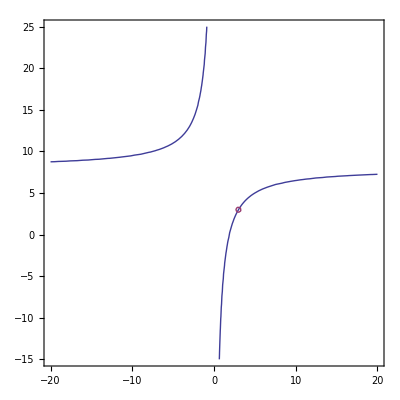

```mathematica
ContourPlot[{(y-8) x+15==0,(x-3)^2+(y-3)^2==.1},{x,-20,20},{y,-15,25}]
```

```mathematica
Show[{
ListPlot[{{4.25,4.47059},{4.47059,4.64474},{4.64474,4.77054},{4.77054,4.8557},{4.8557,4.91085},{4.91085,4.94554},{4.94554,4.96696},{4.96696,4.98005},{4.98005,4.98798},{4.98798,4.99284},{4.99284,4.9971},{4.9971,5.02619},{5.02619,5.57149},{5.57149,15.2844}},PlotStyle->PointSize[Large]],
ContourPlot[{(y-8) x+15==0,(x-3)^2+(y-3)^2==.04},{x,-8,13},{y,-5,16}]
},AspectRatio->Automatic]
```

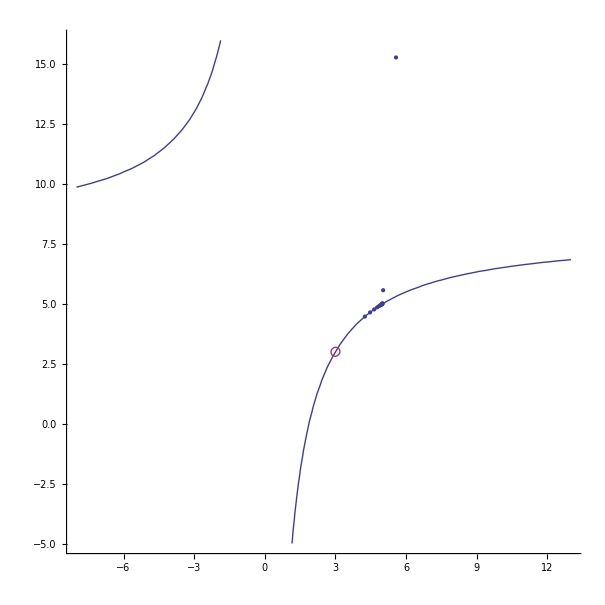

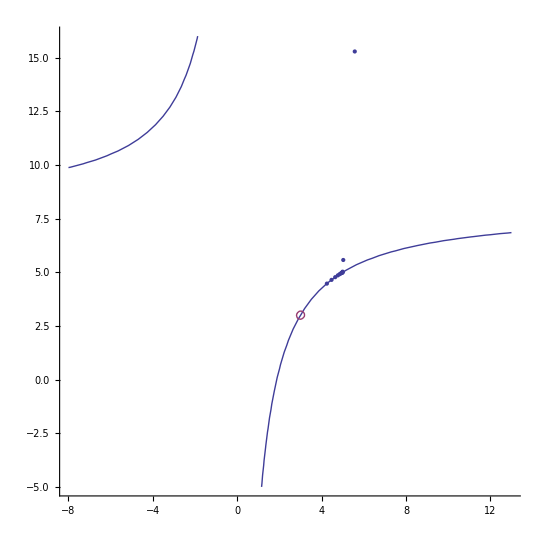

```mathematica
ListDensityPlot[{{-8,-5,6},{-8,-4.75,6},{-8,-4.5,6},{-8,-4.25,6},{-8,-4,6},{-8,-3.75,6},{-8,-3.5,6},{-8,-3.25,6},{-8,-3,6},{-8,-2.75,6},{-8,-2.5,6},{-8,-2.25,6},{-8,-2,6},{-8,-1.75,6},{-8,-1.5,6},{-8,-1.25,6},{-8,-1,6},{-8,-0.75,6},{-8,-0.5,6},{-8,-0.25,6},{-8,0,3},{-8,0.25,6},{-8,0.5,7},{-8,0.75,7},{-8,1,7},{-8,1.25,7},{-8,1.5,7},{-8,1.75,7},{-8,2,7},{-8,2.25,7},{-8,2.5,7},{-8,2.75,7},{-8,3,7},{-8,3.25,7},{-8,3.5,7},{-8,3.75,7},{-8,4,7},{-8,4.25,7},{-8,4.5,7},{-8,4.75,7},{-8,5,7},{-8,5.25,7},{-8,5.5,7},{-8,5.75,7},{-8,6,7},{-8,6.25,7},{-8,6.5,7},{-8,6.75,7},{-8,7,7},{-8,7.25,7},{-8,7.5,7},{-8,7.75,7},{-8,8,7},{-8,8.25,7},{-8,8.5,7},{-8,8.75,7},{-8,9,7},{-8,9.25,7},{-8,9.5,8},{-8,9.75,8},{-8,10,8},{-8,10.25,8},{-8,10.5,7},{-8,10.75,7},{-8,11,7},{-8,11.25,7},{-8,11.5,7},{-8,11.75,7},{-8,12,7},{-8,12.25,7},{-8,12.5,7},{-8,12.75,7},{-8,13,7},{-8,13.25,7},{-8,13.5,7},{-8,13.75,7},{-8,14,7},{-8,14.25,7},{-8,14.5,7},{-8,14.75,7},{-8,15,7},{-8,15.25,7},{-8,15.5,7},{-8,15.75,7},{-7.75,-5,6},{-7.75,-4.75,6},{-7.75,-4.5,6},{-7.75,-4.25,6},{-7.75,-4,6},{-7.75,-3.75,6},{-7.75,-3.5,6},{-7.75,-3.25,6},{-7.75,-3,6},{-7.75,-2.75,6},{-7.75,-2.5,6},{-7.75,-2.25,6},{-7.75,-2,6},{-7.75,-1.75,6},{-7.75,-1.5,6},{-7.75,-1.25,6},{-7.75,-1,6},{-7.75,-0.75,6},{-7.75,-0.5,6},{-7.75,-0.25,6},{-7.75,0,3},{-7.75,0.25,6},{-7.75,0.5,7},{-7.75,0.75,7},{-7.75,1,7},{-7.75,1.25,7},{-7.75,1.5,7},{-7.75,1.75,7},{-7.75,2,7},{-7.75,2.25,7},{-7.75,2.5,7},{-7.75,2.75,7},{-7.75,3,7},{-7.75,3.25,7},{-7.75,3.5,7},{-7.75,3.75,7},{-7.75,4,7},{-7.75,4.25,7},{-7.75,4.5,7},{-7.75,4.75,7},{-7.75,5,7},{-7.75,5.25,7},{-7.75,5.5,7},{-7.75,5.75,7},{-7.75,6,7},{-7.75,6.25,7},{-7.75,6.5,7},{-7.75,6.75,7},{-7.75,7,7},{-7.75,7.25,7},{-7.75,7.5,7},{-7.75,7.75,7},{-7.75,8,7},{-7.75,8.25,7},{-7.75,8.5,7},{-7.75,8.75,7},{-7.75,9,7},{-7.75,9.25,7},{-7.75,9.5,8},{-7.75,9.75,8},{-7.75,10,8},{-7.75,10.25,8},{-7.75,10.5,7},{-7.75,10.75,7},{-7.75,11,7},{-7.75,11.25,7},{-7.75,11.5,7},{-7.75,11.75,7},{-7.75,12,7},{-7.75,12.25,7},{-7.75,12.5,7},{-7.75,12.75,7},{-7.75,13,7},{-7.75,13.25,7},{-7.75,13.5,7},{-7.75,13.75,7},{-7.75,14,7},{-7.75,14.25,7},{-7.75,14.5,7},{-7.75,14.75,7},{-7.75,15,7},{-7.75,15.25,7},{-7.75,15.5,7},{-7.75,15.75,7},{-7.5,-5,6},{-7.5,-4.75,6},{-7.5,-4.5,6},{-7.5,-4.25,6},{-7.5,-4,6},{-7.5,-3.75,6},{-7.5,-3.5,6},{-7.5,-3.25,6},{-7.5,-3,6},{-7.5,-2.75,6},{-7.5,-2.5,6},{-7.5,-2.25,6},{-7.5,-2,6},{-7.5,-1.75,6},{-7.5,-1.5,6},{-7.5,-1.25,6},{-7.5,-1,6},{-7.5,-0.75,6},{-7.5,-0.5,6},{-7.5,-0.25,6},{-7.5,0,3},{-7.5,0.25,6},{-7.5,0.5,7},{-7.5,0.75,7},{-7.5,1,7},{-7.5,1.25,7},{-7.5,1.5,7},{-7.5,1.75,7},{-7.5,2,7},{-7.5,2.25,7},{-7.5,2.5,7},{-7.5,2.75,7},{-7.5,3,7},{-7.5,3.25,7},{-7.5,3.5,7},{-7.5,3.75,7},{-7.5,4,7},{-7.5,4.25,7},{-7.5,4.5,7},{-7.5,4.75,7},{-7.5,5,7},{-7.5,5.25,7},{-7.5,5.5,7},{-7.5,5.75,7},{-7.5,6,7},{-7.5,6.25,7},{-7.5,6.5,7},{-7.5,6.75,7},{-7.5,7,7},{-7.5,7.25,7},{-7.5,7.5,7},{-7.5,7.75,7},{-7.5,8,7},{-7.5,8.25,7},{-7.5,8.5,7},{-7.5,8.75,7},{-7.5,9,7},{-7.5,9.25,7},{-7.5,9.5,7},{-7.5,9.75,8},{-7.5,10,20},{-7.5,10.25,8},{-7.5,10.5,7},{-7.5,10.75,7},{-7.5,11,7},{-7.5,11.25,7},{-7.5,11.5,7},{-7.5,11.75,7},{-7.5,12,7},{-7.5,12.25,7},{-7.5,12.5,7},{-7.5,12.75,7},{-7.5,13,7},{-7.5,13.25,7},{-7.5,13.5,7},{-7.5,13.75,7},{-7.5,14,7},{-7.5,14.25,7},{-7.5,14.5,7},{-7.5,14.75,7},{-7.5,15,7},{-7.5,15.25,7},{-7.5,15.5,7},{-7.5,15.75,7},{-7.25,-5,6},{-7.25,-4.75,6},{-7.25,-4.5,6},{-7.25,-4.25,6},{-7.25,-4,6},{-7.25,-3.75,6},{-7.25,-3.5,6},{-7.25,-3.25,6},{-7.25,-3,6},{-7.25,-2.75,6},{-7.25,-2.5,6},{-7.25,-2.25,6},{-7.25,-2,6},{-7.25,-1.75,6},{-7.25,-1.5,6},{-7.25,-1.25,6},{-7.25,-1,6},{-7.25,-0.75,6},{-7.25,-0.5,6},{-7.25,-0.25,6},{-7.25,0,3},{-7.25,0.25,6},{-7.25,0.5,7},{-7.25,0.75,7},{-7.25,1,7},{-7.25,1.25,7},{-7.25,1.5,7},{-7.25,1.75,7},{-7.25,2,7},{-7.25,2.25,7},{-7.25,2.5,7},{-7.25,2.75,7},{-7.25,3,7},{-7.25,3.25,7},{-7.25,3.5,7},{-7.25,3.75,7},{-7.25,4,7},{-7.25,4.25,7},{-7.25,4.5,7},{-7.25,4.75,7},{-7.25,5,7},{-7.25,5.25,7},{-7.25,5.5,7},{-7.25,5.75,7},{-7.25,6,7},{-7.25,6.25,7},{-7.25,6.5,7},{-7.25,6.75,7},{-7.25,7,7},{-7.25,7.25,7},{-7.25,7.5,7},{-7.25,7.75,7},{-7.25,8,7},{-7.25,8.25,7},{-7.25,8.5,7},{-7.25,8.75,7},{-7.25,9,7},{-7.25,9.25,7},{-7.25,9.5,7},{-7.25,9.75,8},{-7.25,10,8},{-7.25,10.25,8},{-7.25,10.5,8},{-7.25,10.75,7},{-7.25,11,7},{-7.25,11.25,7},{-7.25,11.5,7},{-7.25,11.75,7},{-7.25,12,7},{-7.25,12.25,7},{-7.25,12.5,7},{-7.25,12.75,7},{-7.25,13,7},{-7.25,13.25,7},{-7.25,13.5,7},{-7.25,13.75,7},{-7.25,14,7},{-7.25,14.25,7},{-7.25,14.5,7},{-7.25,14.75,7},{-7.25,15,7},{-7.25,15.25,7},{-7.25,15.5,7},{-7.25,15.75,7},{-7,-5,6},{-7,-4.75,6},{-7,-4.5,6},{-7,-4.25,6},{-7,-4,6},{-7,-3.75,6},{-7,-3.5,6},{-7,-3.25,6},{-7,-3,6},{-7,-2.75,6},{-7,-2.5,6},{-7,-2.25,6},{-7,-2,6},{-7,-1.75,6},{-7,-1.5,6},{-7,-1.25,6},{-7,-1,6},{-7,-0.75,6},{-7,-0.5,6},{-7,-0.25,6},{-7,0,3},{-7,0.25,6},{-7,0.5,7},{-7,0.75,7},{-7,1,7},{-7,1.25,7},{-7,1.5,7},{-7,1.75,7},{-7,2,7},{-7,2.25,7},{-7,2.5,7},{-7,2.75,7},{-7,3,7},{-7,3.25,7},{-7,3.5,7},{-7,3.75,7},{-7,4,7},{-7,4.25,7},{-7,4.5,7},{-7,4.75,7},{-7,5,7},{-7,5.25,7},{-7,5.5,7},{-7,5.75,7},{-7,6,7},{-7,6.25,7},{-7,6.5,7},{-7,6.75,7},{-7,7,7},{-7,7.25,7},{-7,7.5,7},{-7,7.75,7},{-7,8,7},{-7,8.25,7},{-7,8.5,7},{-7,8.75,7},{-7,9,7},{-7,9.25,7},{-7,9.5,7},{-7,9.75,8},{-7,10,8},{-7,10.25,8},{-7,10.5,8},{-7,10.75,7},{-7,11,7},{-7,11.25,7},{-7,11.5,7},{-7,11.75,7},{-7,12,7},{-7,12.25,7},{-7,12.5,7},{-7,12.75,7},{-7,13,7},{-7,13.25,7},{-7,13.5,7},{-7,13.75,7},{-7,14,7},{-7,14.25,7},{-7,14.5,7},{-7,14.75,7},{-7,15,7},{-7,15.25,7},{-7,15.5,7},{-7,15.75,7},{-6.75,-5,6},{-6.75,-4.75,6},{-6.75,-4.5,6},{-6.75,-4.25,6},{-6.75,-4,6},{-6.75,-3.75,6},{-6.75,-3.5,6},{-6.75,-3.25,6},{-6.75,-3,6},{-6.75,-2.75,6},{-6.75,-2.5,6},{-6.75,-2.25,6},{-6.75,-2,6},{-6.75,-1.75,6},{-6.75,-1.5,6},{-6.75,-1.25,6},{-6.75,-1,6},{-6.75,-0.75,6},{-6.75,-0.5,6},{-6.75,-0.25,6},{-6.75,0,3},{-6.75,0.25,7},{-6.75,0.5,7},{-6.75,0.75,7},{-6.75,1,7},{-6.75,1.25,7},{-6.75,1.5,7},{-6.75,1.75,7},{-6.75,2,7},{-6.75,2.25,7},{-6.75,2.5,7},{-6.75,2.75,7},{-6.75,3,7},{-6.75,3.25,7},{-6.75,3.5,7},{-6.75,3.75,7},{-6.75,4,7},{-6.75,4.25,7},{-6.75,4.5,7},{-6.75,4.75,7},{-6.75,5,7},{-6.75,5.25,7},{-6.75,5.5,7},{-6.75,5.75,7},{-6.75,6,7},{-6.75,6.25,7},{-6.75,6.5,7},{-6.75,6.75,7},{-6.75,7,7},{-6.75,7.25,7},{-6.75,7.5,7},{-6.75,7.75,7},{-6.75,8,7},{-6.75,8.25,7},{-6.75,8.5,7},{-6.75,8.75,7},{-6.75,9,7},{-6.75,9.25,7},{-6.75,9.5,7},{-6.75,9.75,8},{-6.75,10,8},{-6.75,10.25,8},{-6.75,10.5,8},{-6.75,10.75,7},{-6.75,11,7},{-6.75,11.25,7},{-6.75,11.5,7},{-6.75,11.75,7},{-6.75,12,7},{-6.75,12.25,7},{-6.75,12.5,7},{-6.75,12.75,7},{-6.75,13,7},{-6.75,13.25,7},{-6.75,13.5,7},{-6.75,13.75,7},{-6.75,14,7},{-6.75,14.25,7},{-6.75,14.5,7},{-6.75,14.75,7},{-6.75,15,7},{-6.75,15.25,7},{-6.75,15.5,7},{-6.75,15.75,7},{-6.5,-5,6},{-6.5,-4.75,6},{-6.5,-4.5,6},{-6.5,-4.25,6},{-6.5,-4,6},{-6.5,-3.75,6},{-6.5,-3.5,6},{-6.5,-3.25,6},{-6.5,-3,6},{-6.5,-2.75,6},{-6.5,-2.5,6},{-6.5,-2.25,6},{-6.5,-2,6},{-6.5,-1.75,6},{-6.5,-1.5,6},{-6.5,-1.25,6},{-6.5,-1,6},{-6.5,-0.75,6},{-6.5,-0.5,6},{-6.5,-0.25,6},{-6.5,0,3},{-6.5,0.25,7},{-6.5,0.5,7},{-6.5,0.75,7},{-6.5,1,7},{-6.5,1.25,7},{-6.5,1.5,7},{-6.5,1.75,7},{-6.5,2,7},{-6.5,2.25,7},{-6.5,2.5,7},{-6.5,2.75,7},{-6.5,3,7},{-6.5,3.25,7},{-6.5,3.5,7},{-6.5,3.75,7},{-6.5,4,7},{-6.5,4.25,7},{-6.5,4.5,7},{-6.5,4.75,7},{-6.5,5,7},{-6.5,5.25,7},{-6.5,5.5,7},{-6.5,5.75,7},{-6.5,6,7},{-6.5,6.25,7},{-6.5,6.5,7},{-6.5,6.75,7},{-6.5,7,7},{-6.5,7.25,7},{-6.5,7.5,7},{-6.5,7.75,7},{-6.5,8,7},{-6.5,8.25,7},{-6.5,8.5,7},{-6.5,8.75,7},{-6.5,9,7},{-6.5,9.25,7},{-6.5,9.5,7},{-6.5,9.75,7},{-6.5,10,8},{-6.5,10.25,8},{-6.5,10.5,8},{-6.5,10.75,8},{-6.5,11,7},{-6.5,11.25,7},{-6.5,11.5,7},{-6.5,11.75,7},{-6.5,12,7},{-6.5,12.25,7},{-6.5,12.5,7},{-6.5,12.75,7},{-6.5,13,7},{-6.5,13.25,7},{-6.5,13.5,7},{-6.5,13.75,7},{-6.5,14,7},{-6.5,14.25,7},{-6.5,14.5,7},{-6.5,14.75,7},{-6.5,15,7},{-6.5,15.25,7},{-6.5,15.5,7},{-6.5,15.75,7},{-6.25,-5,6},{-6.25,-4.75,6},{-6.25,-4.5,6},{-6.25,-4.25,6},{-6.25,-4,6},{-6.25,-3.75,6},{-6.25,-3.5,6},{-6.25,-3.25,6},{-6.25,-3,6},{-6.25,-2.75,6},{-6.25,-2.5,6},{-6.25,-2.25,6},{-6.25,-2,6},{-6.25,-1.75,6},{-6.25,-1.5,6},{-6.25,-1.25,6},{-6.25,-1,6},{-6.25,-0.75,6},{-6.25,-0.5,6},{-6.25,-0.25,6},{-6.25,0,3},{-6.25,0.25,7},{-6.25,0.5,7},{-6.25,0.75,7},{-6.25,1,7},{-6.25,1.25,7},{-6.25,1.5,7},{-6.25,1.75,7},{-6.25,2,7},{-6.25,2.25,7},{-6.25,2.5,7},{-6.25,2.75,7},{-6.25,3,7},{-6.25,3.25,7},{-6.25,3.5,7},{-6.25,3.75,7},{-6.25,4,7},{-6.25,4.25,7},{-6.25,4.5,7},{-6.25,4.75,7},{-6.25,5,7},{-6.25,5.25,7},{-6.25,5.5,7},{-6.25,5.75,7},{-6.25,6,7},{-6.25,6.25,7},{-6.25,6.5,7},{-6.25,6.75,7},{-6.25,7,7},{-6.25,7.25,7},{-6.25,7.5,7},{-6.25,7.75,7},{-6.25,8,7},{-6.25,8.25,7},{-6.25,8.5,7},{-6.25,8.75,7},{-6.25,9,7},{-6.25,9.25,7},{-6.25,9.5,7},{-6.25,9.75,7},{-6.25,10,8},{-6.25,10.25,8},{-6.25,10.5,8},{-6.25,10.75,8},{-6.25,11,7},{-6.25,11.25,7},{-6.25,11.5,7},{-6.25,11.75,7},{-6.25,12,7},{-6.25,12.25,7},{-6.25,12.5,7},{-6.25,12.75,7},{-6.25,13,7},{-6.25,13.25,7},{-6.25,13.5,7},{-6.25,13.75,7},{-6.25,14,7},{-6.25,14.25,7},{-6.25,14.5,7},{-6.25,14.75,7},{-6.25,15,7},{-6.25,15.25,7},{-6.25,15.5,7},{-6.25,15.75,7},{-6,-5,6},{-6,-4.75,6},{-6,-4.5,6},{-6,-4.25,6},{-6,-4,6},{-6,-3.75,6},{-6,-3.5,6},{-6,-3.25,6},{-6,-3,6},{-6,-2.75,6},{-6,-2.5,6},{-6,-2.25,6},{-6,-2,6},{-6,-1.75,6},{-6,-1.5,6},{-6,-1.25,6},{-6,-1,6},{-6,-0.75,6},{-6,-0.5,6},{-6,-0.25,6},{-6,0,3},{-6,0.25,7},{-6,0.5,7},{-6,0.75,7},{-6,1,7},{-6,1.25,7},{-6,1.5,7},{-6,1.75,7},{-6,2,7},{-6,2.25,7},{-6,2.5,7},{-6,2.75,7},{-6,3,7},{-6,3.25,7},{-6,3.5,7},{-6,3.75,7},{-6,4,7},{-6,4.25,7},{-6,4.5,7},{-6,4.75,7},{-6,5,7},{-6,5.25,7},{-6,5.5,7},{-6,5.75,7},{-6,6,7},{-6,6.25,7},{-6,6.5,7},{-6,6.75,7},{-6,7,7},{-6,7.25,7},{-6,7.5,7},{-6,7.75,7},{-6,8,7},{-6,8.25,7},{-6,8.5,7},{-6,8.75,7},{-6,9,7},{-6,9.25,7},{-6,9.5,7},{-6,9.75,7},{-6,10,7},{-6,10.25,8},{-6,10.5,20},{-6,10.75,8},{-6,11,7},{-6,11.25,7},{-6,11.5,7},{-6,11.75,7},{-6,12,7},{-6,12.25,7},{-6,12.5,7},{-6,12.75,7},{-6,13,7},{-6,13.25,7},{-6,13.5,7},{-6,13.75,7},{-6,14,7},{-6,14.25,7},{-6,14.5,7},{-6,14.75,7},{-6,15,7},{-6,15.25,7},{-6,15.5,7},{-6,15.75,7},{-5.75,-5,6},{-5.75,-4.75,6},{-5.75,-4.5,6},{-5.75,-4.25,6},{-5.75,-4,6},{-5.75,-3.75,6},{-5.75,-3.5,6},{-5.75,-3.25,6},{-5.75,-3,6},{-5.75,-2.75,6},{-5.75,-2.5,6},{-5.75,-2.25,6},{-5.75,-2,6},{-5.75,-1.75,6},{-5.75,-1.5,6},{-5.75,-1.25,6},{-5.75,-1,6},{-5.75,-0.75,6},{-5.75,-0.5,6},{-5.75,-0.25,6},{-5.75,0,3},{-5.75,0.25,7},{-5.75,0.5,7},{-5.75,0.75,7},{-5.75,1,7},{-5.75,1.25,7},{-5.75,1.5,7},{-5.75,1.75,7},{-5.75,2,7},{-5.75,2.25,7},{-5.75,2.5,7},{-5.75,2.75,7},{-5.75,3,7},{-5.75,3.25,7},{-5.75,3.5,7},{-5.75,3.75,7},{-5.75,4,7},{-5.75,4.25,7},{-5.75,4.5,7},{-5.75,4.75,7},{-5.75,5,7},{-5.75,5.25,7},{-5.75,5.5,7},{-5.75,5.75,7},{-5.75,6,7},{-5.75,6.25,7},{-5.75,6.5,7},{-5.75,6.75,7},{-5.75,7,7},{-5.75,7.25,7},{-5.75,7.5,7},{-5.75,7.75,7},{-5.75,8,7},{-5.75,8.25,7},{-5.75,8.5,7},{-5.75,8.75,7},{-5.75,9,7},{-5.75,9.25,7},{-5.75,9.5,7},{-5.75,9.75,7},{-5.75,10,7},{-5.75,10.25,8},{-5.75,10.5,8},{-5.75,10.75,8},{-5.75,11,8},{-5.75,11.25,7},{-5.75,11.5,7},{-5.75,11.75,7},{-5.75,12,7},{-5.75,12.25,7},{-5.75,12.5,7},{-5.75,12.75,7},{-5.75,13,7},{-5.75,13.25,7},{-5.75,13.5,7},{-5.75,13.75,7},{-5.75,14,7},{-5.75,14.25,7},{-5.75,14.5,7},{-5.75,14.75,7},{-5.75,15,7},{-5.75,15.25,7},{-5.75,15.5,7},{-5.75,15.75,7},{-5.5,-5,6},{-5.5,-4.75,6},{-5.5,-4.5,6},{-5.5,-4.25,6},{-5.5,-4,6},{-5.5,-3.75,6},{-5.5,-3.5,6},{-5.5,-3.25,6},{-5.5,-3,6},{-5.5,-2.75,6},{-5.5,-2.5,6},{-5.5,-2.25,6},{-5.5,-2,6},{-5.5,-1.75,6},{-5.5,-1.5,6},{-5.5,-1.25,6},{-5.5,-1,6},{-5.5,-0.75,6},{-5.5,-0.5,6},{-5.5,-0.25,6},{-5.5,0,3},{-5.5,0.25,7},{-5.5,0.5,7},{-5.5,0.75,7},{-5.5,1,7},{-5.5,1.25,7},{-5.5,1.5,7},{-5.5,1.75,7},{-5.5,2,7},{-5.5,2.25,7},{-5.5,2.5,7},{-5.5,2.75,7},{-5.5,3,7},{-5.5,3.25,7},{-5.5,3.5,7},{-5.5,3.75,7},{-5.5,4,7},{-5.5,4.25,7},{-5.5,4.5,7},{-5.5,4.75,7},{-5.5,5,7},{-5.5,5.25,7},{-5.5,5.5,7},{-5.5,5.75,7},{-5.5,6,7},{-5.5,6.25,7},{-5.5,6.5,7},{-5.5,6.75,7},{-5.5,7,7},{-5.5,7.25,7},{-5.5,7.5,7},{-5.5,7.75,7},{-5.5,8,7},{-5.5,8.25,7},{-5.5,8.5,7},{-5.5,8.75,7},{-5.5,9,7},{-5.5,9.25,7},{-5.5,9.5,7},{-5.5,9.75,7},{-5.5,10,7},{-5.5,10.25,8},{-5.5,10.5,8},{-5.5,10.75,9},{-5.5,11,8},{-5.5,11.25,7},{-5.5,11.5,7},{-5.5,11.75,7},{-5.5,12,7},{-5.5,12.25,7},{-5.5,12.5,7},{-5.5,12.75,7},{-5.5,13,7},{-5.5,13.25,7},{-5.5,13.5,7},{-5.5,13.75,7},{-5.5,14,7},{-5.5,14.25,7},{-5.5,14.5,7},{-5.5,14.75,7},{-5.5,15,7},{-5.5,15.25,7},{-5.5,15.5,7},{-5.5,15.75,7},{-5.25,-5,6},{-5.25,-4.75,6},{-5.25,-4.5,6},{-5.25,-4.25,6},{-5.25,-4,6},{-5.25,-3.75,6},{-5.25,-3.5,6},{-5.25,-3.25,6},{-5.25,-3,6},{-5.25,-2.75,6},{-5.25,-2.5,6},{-5.25,-2.25,6},{-5.25,-2,6},{-5.25,-1.75,6},{-5.25,-1.5,6},{-5.25,-1.25,6},{-5.25,-1,6},{-5.25,-0.75,6},{-5.25,-0.5,6},{-5.25,-0.25,6},{-5.25,0,3},{-5.25,0.25,7},{-5.25,0.5,7},{-5.25,0.75,7},{-5.25,1,7},{-5.25,1.25,7},{-5.25,1.5,7},{-5.25,1.75,7},{-5.25,2,7},{-5.25,2.25,7},{-5.25,2.5,7},{-5.25,2.75,7},{-5.25,3,7},{-5.25,3.25,7},{-5.25,3.5,7},{-5.25,3.75,7},{-5.25,4,7},{-5.25,4.25,7},{-5.25,4.5,7},{-5.25,4.75,7},{-5.25,5,7},{-5.25,5.25,7},{-5.25,5.5,7},{-5.25,5.75,7},{-5.25,6,7},{-5.25,6.25,7},{-5.25,6.5,7},{-5.25,6.75,7},{-5.25,7,7},{-5.25,7.25,7},{-5.25,7.5,7},{-5.25,7.75,7},{-5.25,8,7},{-5.25,8.25,7},{-5.25,8.5,7},{-5.25,8.75,7},{-5.25,9,7},{-5.25,9.25,7},{-5.25,9.5,7},{-5.25,9.75,7},{-5.25,10,7},{-5.25,10.25,7},{-5.25,10.5,8},{-5.25,10.75,8},{-5.25,11,8},{-5.25,11.25,8},{-5.25,11.5,7},{-5.25,11.75,7},{-5.25,12,7},{-5.25,12.25,7},{-5.25,12.5,7},{-5.25,12.75,7},{-5.25,13,7},{-5.25,13.25,7},{-5.25,13.5,7},{-5.25,13.75,7},{-5.25,14,7},{-5.25,14.25,7},{-5.25,14.5,7},{-5.25,14.75,7},{-5.25,15,7},{-5.25,15.25,7},{-5.25,15.5,7},{-5.25,15.75,7},{-5,-5,6},{-5,-4.75,6},{-5,-4.5,6},{-5,-4.25,6},{-5,-4,6},{-5,-3.75,6},{-5,-3.5,6},{-5,-3.25,6},{-5,-3,6},{-5,-2.75,6},{-5,-2.5,6},{-5,-2.25,6},{-5,-2,6},{-5,-1.75,6},{-5,-1.5,6},{-5,-1.25,6},{-5,-1,6},{-5,-0.75,6},{-5,-0.5,6},{-5,-0.25,6},{-5,0,3},{-5,0.25,7},{-5,0.5,7},{-5,0.75,7},{-5,1,7},{-5,1.25,7},{-5,1.5,7},{-5,1.75,7},{-5,2,7},{-5,2.25,7},{-5,2.5,7},{-5,2.75,7},{-5,3,7},{-5,3.25,7},{-5,3.5,7},{-5,3.75,7},{-5,4,7},{-5,4.25,7},{-5,4.5,7},{-5,4.75,7},{-5,5,7},{-5,5.25,7},{-5,5.5,7},{-5,5.75,7},{-5,6,7},{-5,6.25,7},{-5,6.5,7},{-5,6.75,7},{-5,7,7},{-5,7.25,7},{-5,7.5,7},{-5,7.75,7},{-5,8,7},{-5,8.25,7},{-5,8.5,7},{-5,8.75,7},{-5,9,7},{-5,9.25,7},{-5,9.5,7},{-5,9.75,7},{-5,10,7},{-5,10.25,7},{-5,10.5,8},{-5,10.75,8},{-5,11,20},{-5,11.25,8},{-5,11.5,8},{-5,11.75,7},{-5,12,7},{-5,12.25,7},{-5,12.5,7},{-5,12.75,7},{-5,13,7},{-5,13.25,7},{-5,13.5,7},{-5,13.75,7},{-5,14,7},{-5,14.25,7},{-5,14.5,7},{-5,14.75,7},{-5,15,7},{-5,15.25,7},{-5,15.5,7},{-5,15.75,7},{-4.75,-5,6},{-4.75,-4.75,6},{-4.75,-4.5,6},{-4.75,-4.25,6},{-4.75,-4,6},{-4.75,-3.75,6},{-4.75,-3.5,6},{-4.75,-3.25,6},{-4.75,-3,6},{-4.75,-2.75,6},{-4.75,-2.5,6},{-4.75,-2.25,6},{-4.75,-2,6},{-4.75,-1.75,6},{-4.75,-1.5,6},{-4.75,-1.25,6},{-4.75,-1,6},{-4.75,-0.75,6},{-4.75,-0.5,6},{-4.75,-0.25,6},{-4.75,0,3},{-4.75,0.25,7},{-4.75,0.5,7},{-4.75,0.75,7},{-4.75,1,7},{-4.75,1.25,7},{-4.75,1.5,7},{-4.75,1.75,7},{-4.75,2,7},{-4.75,2.25,7},{-4.75,2.5,7},{-4.75,2.75,7},{-4.75,3,7},{-4.75,3.25,7},{-4.75,3.5,7},{-4.75,3.75,7},{-4.75,4,7},{-4.75,4.25,7},{-4.75,4.5,7},{-4.75,4.75,7},{-4.75,5,7},{-4.75,5.25,7},{-4.75,5.5,7},{-4.75,5.75,7},{-4.75,6,7},{-4.75,6.25,7},{-4.75,6.5,7},{-4.75,6.75,7},{-4.75,7,7},{-4.75,7.25,7},{-4.75,7.5,7},{-4.75,7.75,7},{-4.75,8,7},{-4.75,8.25,7},{-4.75,8.5,7},{-4.75,8.75,7},{-4.75,9,7},{-4.75,9.25,7},{-4.75,9.5,7},{-4.75,9.75,7},{-4.75,10,7},{-4.75,10.25,7},{-4.75,10.5,7},{-4.75,10.75,8},{-4.75,11,8},{-4.75,11.25,8},{-4.75,11.5,8},{-4.75,11.75,7},{-4.75,12,7},{-4.75,12.25,7},{-4.75,12.5,7},{-4.75,12.75,7},{-4.75,13,7},{-4.75,13.25,7},{-4.75,13.5,7},{-4.75,13.75,7},{-4.75,14,7},{-4.75,14.25,7},{-4.75,14.5,7},{-4.75,14.75,7},{-4.75,15,7},{-4.75,15.25,7},{-4.75,15.5,7},{-4.75,15.75,7},{-4.5,-5,6},{-4.5,-4.75,6},{-4.5,-4.5,6},{-4.5,-4.25,6},{-4.5,-4,6},{-4.5,-3.75,6},{-4.5,-3.5,6},{-4.5,-3.25,6},{-4.5,-3,6},{-4.5,-2.75,6},{-4.5,-2.5,6},{-4.5,-2.25,6},{-4.5,-2,6},{-4.5,-1.75,6},{-4.5,-1.5,6},{-4.5,-1.25,6},{-4.5,-1,6},{-4.5,-0.75,6},{-4.5,-0.5,6},{-4.5,-0.25,6},{-4.5,0,3},{-4.5,0.25,7},{-4.5,0.5,7},{-4.5,0.75,7},{-4.5,1,7},{-4.5,1.25,7},{-4.5,1.5,7},{-4.5,1.75,7},{-4.5,2,7},{-4.5,2.25,7},{-4.5,2.5,7},{-4.5,2.75,7},{-4.5,3,7},{-4.5,3.25,7},{-4.5,3.5,7},{-4.5,3.75,7},{-4.5,4,7},{-4.5,4.25,7},{-4.5,4.5,7},{-4.5,4.75,7},{-4.5,5,7},{-4.5,5.25,7},{-4.5,5.5,7},{-4.5,5.75,7},{-4.5,6,7},{-4.5,6.25,7},{-4.5,6.5,7},{-4.5,6.75,7},{-4.5,7,7},{-4.5,7.25,7},{-4.5,7.5,7},{-4.5,7.75,7},{-4.5,8,7},{-4.5,8.25,7},{-4.5,8.5,7},{-4.5,8.75,7},{-4.5,9,7},{-4.5,9.25,7},{-4.5,9.5,7},{-4.5,9.75,7},{-4.5,10,7},{-4.5,10.25,7},{-4.5,10.5,7},{-4.5,10.75,7},{-4.5,11,8},{-4.5,11.25,8},{-4.5,11.5,8},{-4.5,11.75,8},{-4.5,12,7},{-4.5,12.25,7},{-4.5,12.5,7},{-4.5,12.75,7},{-4.5,13,7},{-4.5,13.25,7},{-4.5,13.5,7},{-4.5,13.75,7},{-4.5,14,7},{-4.5,14.25,7},{-4.5,14.5,7},{-4.5,14.75,7},{-4.5,15,7},{-4.5,15.25,7},{-4.5,15.5,7},{-4.5,15.75,7},{-4.25,-5,6},{-4.25,-4.75,6},{-4.25,-4.5,6},{-4.25,-4.25,6},{-4.25,-4,6},{-4.25,-3.75,6},{-4.25,-3.5,6},{-4.25,-3.25,6},{-4.25,-3,6},{-4.25,-2.75,6},{-4.25,-2.5,6},{-4.25,-2.25,6},{-4.25,-2,6},{-4.25,-1.75,6},{-4.25,-1.5,6},{-4.25,-1.25,6},{-4.25,-1,6},{-4.25,-0.75,6},{-4.25,-0.5,6},{-4.25,-0.25,6},{-4.25,0,3},{-4.25,0.25,7},{-4.25,0.5,7},{-4.25,0.75,7},{-4.25,1,7},{-4.25,1.25,7},{-4.25,1.5,7},{-4.25,1.75,7},{-4.25,2,7},{-4.25,2.25,7},{-4.25,2.5,7},{-4.25,2.75,7},{-4.25,3,7},{-4.25,3.25,7},{-4.25,3.5,7},{-4.25,3.75,7},{-4.25,4,7},{-4.25,4.25,7},{-4.25,4.5,7},{-4.25,4.75,7},{-4.25,5,7},{-4.25,5.25,7},{-4.25,5.5,7},{-4.25,5.75,7},{-4.25,6,7},{-4.25,6.25,7},{-4.25,6.5,7},{-4.25,6.75,7},{-4.25,7,7},{-4.25,7.25,7},{-4.25,7.5,7},{-4.25,7.75,7},{-4.25,8,7},{-4.25,8.25,7},{-4.25,8.5,7},{-4.25,8.75,7},{-4.25,9,7},{-4.25,9.25,7},{-4.25,9.5,7},{-4.25,9.75,7},{-4.25,10,7},{-4.25,10.25,7},{-4.25,10.5,7},{-4.25,10.75,7},{-4.25,11,8},{-4.25,11.25,8},{-4.25,11.5,8},{-4.25,11.75,8},{-4.25,12,8},{-4.25,12.25,7},{-4.25,12.5,7},{-4.25,12.75,7},{-4.25,13,7},{-4.25,13.25,7},{-4.25,13.5,7},{-4.25,13.75,7},{-4.25,14,7},{-4.25,14.25,7},{-4.25,14.5,7},{-4.25,14.75,7},{-4.25,15,7},{-4.25,15.25,7},{-4.25,15.5,7},{-4.25,15.75,7},{-4,-5,6},{-4,-4.75,6},{-4,-4.5,6},{-4,-4.25,6},{-4,-4,6},{-4,-3.75,6},{-4,-3.5,6},{-4,-3.25,6},{-4,-3,6},{-4,-2.75,6},{-4,-2.5,6},{-4,-2.25,6},{-4,-2,6},{-4,-1.75,6},{-4,-1.5,6},{-4,-1.25,6},{-4,-1,6},{-4,-0.75,6},{-4,-0.5,6},{-4,-0.25,7},{-4,0,3},{-4,0.25,7},{-4,0.5,7},{-4,0.75,7},{-4,1,7},{-4,1.25,7},{-4,1.5,7},{-4,1.75,7},{-4,2,7},{-4,2.25,7},{-4,2.5,7},{-4,2.75,7},{-4,3,7},{-4,3.25,7},{-4,3.5,7},{-4,3.75,7},{-4,4,7},{-4,4.25,7},{-4,4.5,7},{-4,4.75,7},{-4,5,7},{-4,5.25,7},{-4,5.5,7},{-4,5.75,7},{-4,6,7},{-4,6.25,7},{-4,6.5,7},{-4,6.75,7},{-4,7,7},{-4,7.25,7},{-4,7.5,7},{-4,7.75,7},{-4,8,7},{-4,8.25,7},{-4,8.5,7},{-4,8.75,7},{-4,9,7},{-4,9.25,7},{-4,9.5,7},{-4,9.75,7},{-4,10,7},{-4,10.25,7},{-4,10.5,7},{-4,10.75,7},{-4,11,7},{-4,11.25,8},{-4,11.5,8},{-4,11.75,20},{-4,12,8},{-4,12.25,8},{-4,12.5,7},{-4,12.75,7},{-4,13,7},{-4,13.25,7},{-4,13.5,7},{-4,13.75,7},{-4,14,7},{-4,14.25,7},{-4,14.5,7},{-4,14.75,7},{-4,15,7},{-4,15.25,7},{-4,15.5,7},{-4,15.75,7},{-3.75,-5,6},{-3.75,-4.75,6},{-3.75,-4.5,6},{-3.75,-4.25,6},{-3.75,-4,6},{-3.75,-3.75,6},{-3.75,-3.5,6},{-3.75,-3.25,6},{-3.75,-3,6},{-3.75,-2.75,6},{-3.75,-2.5,6},{-3.75,-2.25,6},{-3.75,-2,6},{-3.75,-1.75,6},{-3.75,-1.5,6},{-3.75,-1.25,6},{-3.75,-1,6},{-3.75,-0.75,6},{-3.75,-0.5,6},{-3.75,-0.25,7},{-3.75,0,3},{-3.75,0.25,7},{-3.75,0.5,7},{-3.75,0.75,7},{-3.75,1,7},{-3.75,1.25,7},{-3.75,1.5,7},{-3.75,1.75,7},{-3.75,2,7},{-3.75,2.25,7},{-3.75,2.5,7},{-3.75,2.75,7},{-3.75,3,7},{-3.75,3.25,7},{-3.75,3.5,7},{-3.75,3.75,7},{-3.75,4,7},{-3.75,4.25,7},{-3.75,4.5,7},{-3.75,4.75,7},{-3.75,5,7},{-3.75,5.25,7},{-3.75,5.5,7},{-3.75,5.75,7},{-3.75,6,7},{-3.75,6.25,7},{-3.75,6.5,7},{-3.75,6.75,7},{-3.75,7,7},{-3.75,7.25,7},{-3.75,7.5,7},{-3.75,7.75,7},{-3.75,8,7},{-3.75,8.25,7},{-3.75,8.5,7},{-3.75,8.75,7},{-3.75,9,7},{-3.75,9.25,7},{-3.75,9.5,7},{-3.75,9.75,7},{-3.75,10,7},{-3.75,10.25,7},{-3.75,10.5,7},{-3.75,10.75,7},{-3.75,11,7},{-3.75,11.25,4},{-3.75,11.5,8},{-3.75,11.75,8},{-3.75,12,20},{-3.75,12.25,8},{-3.75,12.5,8},{-3.75,12.75,7},{-3.75,13,7},{-3.75,13.25,7},{-3.75,13.5,7},{-3.75,13.75,7},{-3.75,14,7},{-3.75,14.25,7},{-3.75,14.5,7},{-3.75,14.75,7},{-3.75,15,7},{-3.75,15.25,7},{-3.75,15.5,7},{-3.75,15.75,7},{-3.5,-5,6},{-3.5,-4.75,6},{-3.5,-4.5,6},{-3.5,-4.25,6},{-3.5,-4,6},{-3.5,-3.75,6},{-3.5,-3.5,6},{-3.5,-3.25,6},{-3.5,-3,6},{-3.5,-2.75,6},{-3.5,-2.5,6},{-3.5,-2.25,6},{-3.5,-2,6},{-3.5,-1.75,6},{-3.5,-1.5,6},{-3.5,-1.25,6},{-3.5,-1,6},{-3.5,-0.75,6},{-3.5,-0.5,7},{-3.5,-0.25,7},{-3.5,0,3},{-3.5,0.25,7},{-3.5,0.5,7},{-3.5,0.75,7},{-3.5,1,7},{-3.5,1.25,7},{-3.5,1.5,7},{-3.5,1.75,7},{-3.5,2,7},{-3.5,2.25,7},{-3.5,2.5,7},{-3.5,2.75,7},{-3.5,3,7},{-3.5,3.25,7},{-3.5,3.5,7},{-3.5,3.75,7},{-3.5,4,7},{-3.5,4.25,7},{-3.5,4.5,7},{-3.5,4.75,7},{-3.5,5,7},{-3.5,5.25,7},{-3.5,5.5,7},{-3.5,5.75,7},{-3.5,6,7},{-3.5,6.25,7},{-3.5,6.5,7},{-3.5,6.75,7},{-3.5,7,7},{-3.5,7.25,7},{-3.5,7.5,7},{-3.5,7.75,7},{-3.5,8,7},{-3.5,8.25,7},{-3.5,8.5,7},{-3.5,8.75,7},{-3.5,9,7},{-3.5,9.25,7},{-3.5,9.5,7},{-3.5,9.75,7},{-3.5,10,7},{-3.5,10.25,7},{-3.5,10.5,7},{-3.5,10.75,7},{-3.5,11,7},{-3.5,11.25,7},{-3.5,11.5,7},{-3.5,11.75,8},{-3.5,12,8},{-3.5,12.25,8},{-3.5,12.5,8},{-3.5,12.75,8},{-3.5,13,7},{-3.5,13.25,7},{-3.5,13.5,7},{-3.5,13.75,7},{-3.5,14,7},{-3.5,14.25,7},{-3.5,14.5,7},{-3.5,14.75,7},{-3.5,15,7},{-3.5,15.25,7},{-3.5,15.5,7},{-3.5,15.75,7},{-3.25,-5,6},{-3.25,-4.75,6},{-3.25,-4.5,6},{-3.25,-4.25,6},{-3.25,-4,6},{-3.25,-3.75,6},{-3.25,-3.5,6},{-3.25,-3.25,6},{-3.25,-3,6},{-3.25,-2.75,6},{-3.25,-2.5,6},{-3.25,-2.25,6},{-3.25,-2,6},{-3.25,-1.75,6},{-3.25,-1.5,6},{-3.25,-1.25,6},{-3.25,-1,6},{-3.25,-0.75,6},{-3.25,-0.5,7},{-3.25,-0.25,7},{-3.25,0,3},{-3.25,0.25,7},{-3.25,0.5,7},{-3.25,0.75,7},{-3.25,1,7},{-3.25,1.25,7},{-3.25,1.5,7},{-3.25,1.75,7},{-3.25,2,7},{-3.25,2.25,7},{-3.25,2.5,7},{-3.25,2.75,7},{-3.25,3,7},{-3.25,3.25,7},{-3.25,3.5,7},{-3.25,3.75,7},{-3.25,4,7},{-3.25,4.25,7},{-3.25,4.5,7},{-3.25,4.75,7},{-3.25,5,7},{-3.25,5.25,7},{-3.25,5.5,7},{-3.25,5.75,7},{-3.25,6,7},{-3.25,6.25,7},{-3.25,6.5,7},{-3.25,6.75,7},{-3.25,7,7},{-3.25,7.25,7},{-3.25,7.5,7},{-3.25,7.75,7},{-3.25,8,7},{-3.25,8.25,7},{-3.25,8.5,7},{-3.25,8.75,7},{-3.25,9,7},{-3.25,9.25,7},{-3.25,9.5,7},{-3.25,9.75,7},{-3.25,10,7},{-3.25,10.25,7},{-3.25,10.5,7},{-3.25,10.75,7},{-3.25,11,7},{-3.25,11.25,7},{-3.25,11.5,7},{-3.25,11.75,7},{-3.25,12,8},{-3.25,12.25,8},{-3.25,12.5,8},{-3.25,12.75,8},{-3.25,13,8},{-3.25,13.25,7},{-3.25,13.5,7},{-3.25,13.75,7},{-3.25,14,7},{-3.25,14.25,7},{-3.25,14.5,7},{-3.25,14.75,7},{-3.25,15,7},{-3.25,15.25,7},{-3.25,15.5,7},{-3.25,15.75,7},{-3,-5,6},{-3,-4.75,6},{-3,-4.5,6},{-3,-4.25,6},{-3,-4,6},{-3,-3.75,6},{-3,-3.5,6},{-3,-3.25,6},{-3,-3,6},{-3,-2.75,6},{-3,-2.5,6},{-3,-2.25,6},{-3,-2,6},{-3,-1.75,6},{-3,-1.5,6},{-3,-1.25,6},{-3,-1,6},{-3,-0.75,7},{-3,-0.5,7},{-3,-0.25,7},{-3,0,3},{-3,0.25,7},{-3,0.5,7},{-3,0.75,7},{-3,1,7},{-3,1.25,7},{-3,1.5,7},{-3,1.75,7},{-3,2,7},{-3,2.25,7},{-3,2.5,7},{-3,2.75,7},{-3,3,7},{-3,3.25,7},{-3,3.5,7},{-3,3.75,7},{-3,4,7},{-3,4.25,7},{-3,4.5,7},{-3,4.75,7},{-3,5,7},{-3,5.25,7},{-3,5.5,7},{-3,5.75,7},{-3,6,7},{-3,6.25,7},{-3,6.5,7},{-3,6.75,7},{-3,7,7},{-3,7.25,7},{-3,7.5,7},{-3,7.75,7},{-3,8,7},{-3,8.25,7},{-3,8.5,7},{-3,8.75,7},{-3,9,7},{-3,9.25,7},{-3,9.5,7},{-3,9.75,7},{-3,10,7},{-3,10.25,7},{-3,10.5,7},{-3,10.75,7},{-3,11,7},{-3,11.25,7},{-3,11.5,7},{-3,11.75,7},{-3,12,7},{-3,12.25,7},{-3,12.5,8},{-3,12.75,8},{-3,13,20},{-3,13.25,8},{-3,13.5,8},{-3,13.75,7},{-3,14,7},{-3,14.25,7},{-3,14.5,7},{-3,14.75,7},{-3,15,7},{-3,15.25,7},{-3,15.5,7},{-3,15.75,7},{-2.75,-5,6},{-2.75,-4.75,6},{-2.75,-4.5,6},{-2.75,-4.25,6},{-2.75,-4,6},{-2.75,-3.75,6},{-2.75,-3.5,6},{-2.75,-3.25,6},{-2.75,-3,6},{-2.75,-2.75,6},{-2.75,-2.5,6},{-2.75,-2.25,6},{-2.75,-2,6},{-2.75,-1.75,6},{-2.75,-1.5,6},{-2.75,-1.25,6},{-2.75,-1,6},{-2.75,-0.75,7},{-2.75,-0.5,7},{-2.75,-0.25,7},{-2.75,0,3},{-2.75,0.25,7},{-2.75,0.5,7},{-2.75,0.75,7},{-2.75,1,7},{-2.75,1.25,7},{-2.75,1.5,7},{-2.75,1.75,7},{-2.75,2,7},{-2.75,2.25,7},{-2.75,2.5,7},{-2.75,2.75,7},{-2.75,3,7},{-2.75,3.25,7},{-2.75,3.5,7},{-2.75,3.75,7},{-2.75,4,7},{-2.75,4.25,7},{-2.75,4.5,7},{-2.75,4.75,7},{-2.75,5,7},{-2.75,5.25,7},{-2.75,5.5,7},{-2.75,5.75,7},{-2.75,6,7},{-2.75,6.25,7},{-2.75,6.5,7},{-2.75,6.75,7},{-2.75,7,7},{-2.75,7.25,7},{-2.75,7.5,7},{-2.75,7.75,7},{-2.75,8,7},{-2.75,8.25,7},{-2.75,8.5,7},{-2.75,8.75,7},{-2.75,9,7},{-2.75,9.25,7},{-2.75,9.5,7},{-2.75,9.75,7},{-2.75,10,7},{-2.75,10.25,7},{-2.75,10.5,7},{-2.75,10.75,7},{-2.75,11,7},{-2.75,11.25,7},{-2.75,11.5,7},{-2.75,11.75,7},{-2.75,12,7},{-2.75,12.25,7},{-2.75,12.5,7},{-2.75,12.75,7},{-2.75,13,8},{-2.75,13.25,8},{-2.75,13.5,8},{-2.75,13.75,8},{-2.75,14,8},{-2.75,14.25,7},{-2.75,14.5,7},{-2.75,14.75,7},{-2.75,15,7},{-2.75,15.25,7},{-2.75,15.5,7},{-2.75,15.75,7},{-2.5,-5,6},{-2.5,-4.75,6},{-2.5,-4.5,6},{-2.5,-4.25,6},{-2.5,-4,6},{-2.5,-3.75,6},{-2.5,-3.5,6},{-2.5,-3.25,6},{-2.5,-3,6},{-2.5,-2.75,6},{-2.5,-2.5,6},{-2.5,-2.25,6},{-2.5,-2,6},{-2.5,-1.75,6},{-2.5,-1.5,6},{-2.5,-1.25,6},{-2.5,-1,7},{-2.5,-0.75,7},{-2.5,-0.5,7},{-2.5,-0.25,7},{-2.5,0,3},{-2.5,0.25,7},{-2.5,0.5,7},{-2.5,0.75,7},{-2.5,1,7},{-2.5,1.25,7},{-2.5,1.5,7},{-2.5,1.75,7},{-2.5,2,7},{-2.5,2.25,7},{-2.5,2.5,7},{-2.5,2.75,7},{-2.5,3,7},{-2.5,3.25,7},{-2.5,3.5,7},{-2.5,3.75,7},{-2.5,4,7},{-2.5,4.25,7},{-2.5,4.5,7},{-2.5,4.75,7},{-2.5,5,7},{-2.5,5.25,7},{-2.5,5.5,7},{-2.5,5.75,7},{-2.5,6,7},{-2.5,6.25,7},{-2.5,6.5,7},{-2.5,6.75,7},{-2.5,7,7},{-2.5,7.25,7},{-2.5,7.5,7},{-2.5,7.75,7},{-2.5,8,7},{-2.5,8.25,7},{-2.5,8.5,7},{-2.5,8.75,7},{-2.5,9,7},{-2.5,9.25,7},{-2.5,9.5,7},{-2.5,9.75,7},{-2.5,10,7},{-2.5,10.25,7},{-2.5,10.5,7},{-2.5,10.75,7},{-2.5,11,7},{-2.5,11.25,7},{-2.5,11.5,7},{-2.5,11.75,7},{-2.5,12,7},{-2.5,12.25,7},{-2.5,12.5,7},{-2.5,12.75,7},{-2.5,13,7},{-2.5,13.25,7},{-2.5,13.5,8},{-2.5,13.75,8},{-2.5,14,20},{-2.5,14.25,8},{-2.5,14.5,8},{-2.5,14.75,7},{-2.5,15,7},{-2.5,15.25,7},{-2.5,15.5,7},{-2.5,15.75,7},{-2.25,-5,6},{-2.25,-4.75,6},{-2.25,-4.5,6},{-2.25,-4.25,6},{-2.25,-4,6},{-2.25,-3.75,6},{-2.25,-3.5,6},{-2.25,-3.25,6},{-2.25,-3,6},{-2.25,-2.75,6},{-2.25,-2.5,6},{-2.25,-2.25,6},{-2.25,-2,6},{-2.25,-1.75,6},{-2.25,-1.5,6},{-2.25,-1.25,7},{-2.25,-1,7},{-2.25,-0.75,7},{-2.25,-0.5,7},{-2.25,-0.25,7},{-2.25,0,3},{-2.25,0.25,7},{-2.25,0.5,7},{-2.25,0.75,7},{-2.25,1,7},{-2.25,1.25,7},{-2.25,1.5,7},{-2.25,1.75,7},{-2.25,2,7},{-2.25,2.25,7},{-2.25,2.5,7},{-2.25,2.75,7},{-2.25,3,7},{-2.25,3.25,7},{-2.25,3.5,7},{-2.25,3.75,7},{-2.25,4,7},{-2.25,4.25,7},{-2.25,4.5,7},{-2.25,4.75,7},{-2.25,5,7},{-2.25,5.25,7},{-2.25,5.5,7},{-2.25,5.75,7},{-2.25,6,7},{-2.25,6.25,7},{-2.25,6.5,7},{-2.25,6.75,7},{-2.25,7,7},{-2.25,7.25,7},{-2.25,7.5,7},{-2.25,7.75,7},{-2.25,8,7},{-2.25,8.25,7},{-2.25,8.5,7},{-2.25,8.75,7},{-2.25,9,7},{-2.25,9.25,7},{-2.25,9.5,7},{-2.25,9.75,7},{-2.25,10,7},{-2.25,10.25,7},{-2.25,10.5,7},{-2.25,10.75,7},{-2.25,11,7},{-2.25,11.25,7},{-2.25,11.5,7},{-2.25,11.75,7},{-2.25,12,7},{-2.25,12.25,7},{-2.25,12.5,7},{-2.25,12.75,7},{-2.25,13,7},{-2.25,13.25,7},{-2.25,13.5,7},{-2.25,13.75,7},{-2.25,14,8},{-2.25,14.25,8},{-2.25,14.5,8},{-2.25,14.75,8},{-2.25,15,8},{-2.25,15.25,8},{-2.25,15.5,7},{-2.25,15.75,7},{-2,-5,6},{-2,-4.75,6},{-2,-4.5,6},{-2,-4.25,6},{-2,-4,6},{-2,-3.75,6},{-2,-3.5,6},{-2,-3.25,6},{-2,-3,6},{-2,-2.75,6},{-2,-2.5,6},{-2,-2.25,6},{-2,-2,6},{-2,-1.75,6},{-2,-1.5,7},{-2,-1.25,7},{-2,-1,7},{-2,-0.75,7},{-2,-0.5,7},{-2,-0.25,7},{-2,0,3},{-2,0.25,7},{-2,0.5,7},{-2,0.75,7},{-2,1,7},{-2,1.25,7},{-2,1.5,7},{-2,1.75,7},{-2,2,7},{-2,2.25,7},{-2,2.5,7},{-2,2.75,7},{-2,3,7},{-2,3.25,7},{-2,3.5,7},{-2,3.75,7},{-2,4,7},{-2,4.25,7},{-2,4.5,7},{-2,4.75,7},{-2,5,7},{-2,5.25,7},{-2,5.5,7},{-2,5.75,7},{-2,6,7},{-2,6.25,7},{-2,6.5,7},{-2,6.75,7},{-2,7,7},{-2,7.25,7},{-2,7.5,7},{-2,7.75,7},{-2,8,7},{-2,8.25,7},{-2,8.5,7},{-2,8.75,7},{-2,9,7},{-2,9.25,7},{-2,9.5,7},{-2,9.75,7},{-2,10,7},{-2,10.25,7},{-2,10.5,7},{-2,10.75,7},{-2,11,7},{-2,11.25,7},{-2,11.5,7},{-2,11.75,7},{-2,12,7},{-2,12.25,7},{-2,12.5,7},{-2,12.75,7},{-2,13,7},{-2,13.25,7},{-2,13.5,7},{-2,13.75,7},{-2,14,7},{-2,14.25,7},{-2,14.5,7},{-2,14.75,8},{-2,15,8},{-2,15.25,8},{-2,15.5,20},{-2,15.75,8},{-1.75,-5,6},{-1.75,-4.75,6},{-1.75,-4.5,6},{-1.75,-4.25,6},{-1.75,-4,6},{-1.75,-3.75,6},{-1.75,-3.5,6},{-1.75,-3.25,6},{-1.75,-3,6},{-1.75,-2.75,6},{-1.75,-2.5,6},{-1.75,-2.25,6},{-1.75,-2,7},{-1.75,-1.75,7},{-1.75,-1.5,7},{-1.75,-1.25,7},{-1.75,-1,7},{-1.75,-0.75,7},{-1.75,-0.5,7},{-1.75,-0.25,7},{-1.75,0,3},{-1.75,0.25,7},{-1.75,0.5,7},{-1.75,0.75,7},{-1.75,1,7},{-1.75,1.25,7},{-1.75,1.5,7},{-1.75,1.75,7},{-1.75,2,7},{-1.75,2.25,7},{-1.75,2.5,7},{-1.75,2.75,7},{-1.75,3,7},{-1.75,3.25,7},{-1.75,3.5,7},{-1.75,3.75,7},{-1.75,4,7},{-1.75,4.25,7},{-1.75,4.5,7},{-1.75,4.75,7},{-1.75,5,7},{-1.75,5.25,7},{-1.75,5.5,7},{-1.75,5.75,7},{-1.75,6,7},{-1.75,6.25,7},{-1.75,6.5,7},{-1.75,6.75,7},{-1.75,7,7},{-1.75,7.25,7},{-1.75,7.5,7},{-1.75,7.75,7},{-1.75,8,7},{-1.75,8.25,7},{-1.75,8.5,7},{-1.75,8.75,7},{-1.75,9,7},{-1.75,9.25,7},{-1.75,9.5,7},{-1.75,9.75,7},{-1.75,10,7},{-1.75,10.25,7},{-1.75,10.5,7},{-1.75,10.75,7},{-1.75,11,7},{-1.75,11.25,7},{-1.75,11.5,7},{-1.75,11.75,7},{-1.75,12,7},{-1.75,12.25,7},{-1.75,12.5,7},{-1.75,12.75,7},{-1.75,13,7},{-1.75,13.25,7},{-1.75,13.5,7},{-1.75,13.75,7},{-1.75,14,7},{-1.75,14.25,7},{-1.75,14.5,7},{-1.75,14.75,7},{-1.75,15,7},{-1.75,15.25,7},{-1.75,15.5,7},{-1.75,15.75,8},{-1.5,-5,6},{-1.5,-4.75,6},{-1.5,-4.5,6},{-1.5,-4.25,6},{-1.5,-4,6},{-1.5,-3.75,6},{-1.5,-3.5,6},{-1.5,-3.25,6},{-1.5,-3,6},{-1.5,-2.75,6},{-1.5,-2.5,7},{-1.5,-2.25,7},{-1.5,-2,7},{-1.5,-1.75,7},{-1.5,-1.5,7},{-1.5,-1.25,7},{-1.5,-1,7},{-1.5,-0.75,7},{-1.5,-0.5,7},{-1.5,-0.25,7},{-1.5,0,3},{-1.5,0.25,7},{-1.5,0.5,7},{-1.5,0.75,7},{-1.5,1,7},{-1.5,1.25,7},{-1.5,1.5,7},{-1.5,1.75,7},{-1.5,2,7},{-1.5,2.25,7},{-1.5,2.5,7},{-1.5,2.75,7},{-1.5,3,7},{-1.5,3.25,7},{-1.5,3.5,7},{-1.5,3.75,7},{-1.5,4,7},{-1.5,4.25,7},{-1.5,4.5,7},{-1.5,4.75,7},{-1.5,5,7},{-1.5,5.25,7},{-1.5,5.5,7},{-1.5,5.75,7},{-1.5,6,7},{-1.5,6.25,7},{-1.5,6.5,7},{-1.5,6.75,7},{-1.5,7,7},{-1.5,7.25,7},{-1.5,7.5,7},{-1.5,7.75,7},{-1.5,8,7},{-1.5,8.25,7},{-1.5,8.5,7},{-1.5,8.75,7},{-1.5,9,7},{-1.5,9.25,7},{-1.5,9.5,7},{-1.5,9.75,7},{-1.5,10,7},{-1.5,10.25,7},{-1.5,10.5,7},{-1.5,10.75,7},{-1.5,11,7},{-1.5,11.25,7},{-1.5,11.5,7},{-1.5,11.75,7},{-1.5,12,7},{-1.5,12.25,7},{-1.5,12.5,7},{-1.5,12.75,7},{-1.5,13,7},{-1.5,13.25,7},{-1.5,13.5,7},{-1.5,13.75,7},{-1.5,14,7},{-1.5,14.25,7},{-1.5,14.5,7},{-1.5,14.75,7},{-1.5,15,7},{-1.5,15.25,7},{-1.5,15.5,7},{-1.5,15.75,7},{-1.25,-5,6},{-1.25,-4.75,6},{-1.25,-4.5,6},{-1.25,-4.25,6},{-1.25,-4,6},{-1.25,-3.75,6},{-1.25,-3.5,6},{-1.25,-3.25,6},{-1.25,-3,7},{-1.25,-2.75,7},{-1.25,-2.5,7},{-1.25,-2.25,7},{-1.25,-2,7},{-1.25,-1.75,7},{-1.25,-1.5,7},{-1.25,-1.25,7},{-1.25,-1,7},{-1.25,-0.75,7},{-1.25,-0.5,7},{-1.25,-0.25,7},{-1.25,0,3},{-1.25,0.25,7},{-1.25,0.5,7},{-1.25,0.75,7},{-1.25,1,7},{-1.25,1.25,7},{-1.25,1.5,7},{-1.25,1.75,7},{-1.25,2,7},{-1.25,2.25,7},{-1.25,2.5,7},{-1.25,2.75,7},{-1.25,3,7},{-1.25,3.25,7},{-1.25,3.5,7},{-1.25,3.75,7},{-1.25,4,7},{-1.25,4.25,7},{-1.25,4.5,7},{-1.25,4.75,7},{-1.25,5,7},{-1.25,5.25,7},{-1.25,5.5,7},{-1.25,5.75,7},{-1.25,6,7},{-1.25,6.25,7},{-1.25,6.5,7},{-1.25,6.75,7},{-1.25,7,7},{-1.25,7.25,7},{-1.25,7.5,7},{-1.25,7.75,7},{-1.25,8,7},{-1.25,8.25,7},{-1.25,8.5,7},{-1.25,8.75,7},{-1.25,9,7},{-1.25,9.25,7},{-1.25,9.5,7},{-1.25,9.75,7},{-1.25,10,7},{-1.25,10.25,7},{-1.25,10.5,7},{-1.25,10.75,7},{-1.25,11,7},{-1.25,11.25,7},{-1.25,11.5,7},{-1.25,11.75,7},{-1.25,12,7},{-1.25,12.25,7},{-1.25,12.5,7},{-1.25,12.75,7},{-1.25,13,7},{-1.25,13.25,7},{-1.25,13.5,7},{-1.25,13.75,7},{-1.25,14,7},{-1.25,14.25,7},{-1.25,14.5,7},{-1.25,14.75,7},{-1.25,15,7},{-1.25,15.25,7},{-1.25,15.5,7},{-1.25,15.75,7},{-1,-5,6},{-1,-4.75,6},{-1,-4.5,6},{-1,-4.25,7},{-1,-4,7},{-1,-3.75,7},{-1,-3.5,7},{-1,-3.25,7},{-1,-3,7},{-1,-2.75,7},{-1,-2.5,7},{-1,-2.25,7},{-1,-2,7},{-1,-1.75,7},{-1,-1.5,7},{-1,-1.25,7},{-1,-1,7},{-1,-0.75,7},{-1,-0.5,7},{-1,-0.25,7},{-1,0,3},{-1,0.25,7},{-1,0.5,7},{-1,0.75,7},{-1,1,7},{-1,1.25,7},{-1,1.5,7},{-1,1.75,7},{-1,2,7},{-1,2.25,7},{-1,2.5,7},{-1,2.75,7},{-1,3,7},{-1,3.25,7},{-1,3.5,7},{-1,3.75,7},{-1,4,7},{-1,4.25,7},{-1,4.5,7},{-1,4.75,7},{-1,5,7},{-1,5.25,7},{-1,5.5,7},{-1,5.75,7},{-1,6,7},{-1,6.25,7},{-1,6.5,7},{-1,6.75,7},{-1,7,7},{-1,7.25,7},{-1,7.5,7},{-1,7.75,7},{-1,8,7},{-1,8.25,7},{-1,8.5,7},{-1,8.75,7},{-1,9,7},{-1,9.25,7},{-1,9.5,7},{-1,9.75,7},{-1,10,7},{-1,10.25,7},{-1,10.5,7},{-1,10.75,7},{-1,11,7},{-1,11.25,7},{-1,11.5,7},{-1,11.75,7},{-1,12,7},{-1,12.25,7},{-1,12.5,7},{-1,12.75,7},{-1,13,7},{-1,13.25,7},{-1,13.5,7},{-1,13.75,7},{-1,14,7},{-1,14.25,7},{-1,14.5,7},{-1,14.75,7},{-1,15,7},{-1,15.25,7},{-1,15.5,7},{-1,15.75,7},{-0.75,-5,7},{-0.75,-4.75,7},{-0.75,-4.5,7},{-0.75,-4.25,7},{-0.75,-4,7},{-0.75,-3.75,7},{-0.75,-3.5,7},{-0.75,-3.25,7},{-0.75,-3,7},{-0.75,-2.75,7},{-0.75,-2.5,7},{-0.75,-2.25,7},{-0.75,-2,7},{-0.75,-1.75,7},{-0.75,-1.5,7},{-0.75,-1.25,7},{-0.75,-1,7},{-0.75,-0.75,7},{-0.75,-0.5,7},{-0.75,-0.25,7},{-0.75,0,3},{-0.75,0.25,7},{-0.75,0.5,7},{-0.75,0.75,7},{-0.75,1,7},{-0.75,1.25,7},{-0.75,1.5,7},{-0.75,1.75,7},{-0.75,2,7},{-0.75,2.25,7},{-0.75,2.5,7},{-0.75,2.75,7},{-0.75,3,7},{-0.75,3.25,7},{-0.75,3.5,7},{-0.75,3.75,7},{-0.75,4,7},{-0.75,4.25,7},{-0.75,4.5,7},{-0.75,4.75,7},{-0.75,5,7},{-0.75,5.25,7},{-0.75,5.5,7},{-0.75,5.75,7},{-0.75,6,7},{-0.75,6.25,7},{-0.75,6.5,7},{-0.75,6.75,7},{-0.75,7,7},{-0.75,7.25,7},{-0.75,7.5,7},{-0.75,7.75,7},{-0.75,8,7},{-0.75,8.25,7},{-0.75,8.5,7},{-0.75,8.75,7},{-0.75,9,7},{-0.75,9.25,7},{-0.75,9.5,7},{-0.75,9.75,7},{-0.75,10,7},{-0.75,10.25,7},{-0.75,10.5,7},{-0.75,10.75,7},{-0.75,11,7},{-0.75,11.25,7},{-0.75,11.5,7},{-0.75,11.75,7},{-0.75,12,7},{-0.75,12.25,7},{-0.75,12.5,7},{-0.75,12.75,7},{-0.75,13,7},{-0.75,13.25,7},{-0.75,13.5,7},{-0.75,13.75,7},{-0.75,14,7},{-0.75,14.25,7},{-0.75,14.5,7},{-0.75,14.75,7},{-0.75,15,7},{-0.75,15.25,7},{-0.75,15.5,7},{-0.75,15.75,7},{-0.5,-5,7},{-0.5,-4.75,7},{-0.5,-4.5,7},{-0.5,-4.25,7},{-0.5,-4,7},{-0.5,-3.75,7},{-0.5,-3.5,7},{-0.5,-3.25,7},{-0.5,-3,7},{-0.5,-2.75,7},{-0.5,-2.5,7},{-0.5,-2.25,7},{-0.5,-2,7},{-0.5,-1.75,7},{-0.5,-1.5,7},{-0.5,-1.25,7},{-0.5,-1,7},{-0.5,-0.75,7},{-0.5,-0.5,7},{-0.5,-0.25,7},{-0.5,0,3},{-0.5,0.25,7},{-0.5,0.5,7},{-0.5,0.75,7},{-0.5,1,7},{-0.5,1.25,7},{-0.5,1.5,7},{-0.5,1.75,7},{-0.5,2,7},{-0.5,2.25,7},{-0.5,2.5,7},{-0.5,2.75,7},{-0.5,3,7},{-0.5,3.25,7},{-0.5,3.5,7},{-0.5,3.75,7},{-0.5,4,7},{-0.5,4.25,7},{-0.5,4.5,7},{-0.5,4.75,7},{-0.5,5,7},{-0.5,5.25,7},{-0.5,5.5,7},{-0.5,5.75,7},{-0.5,6,7},{-0.5,6.25,7},{-0.5,6.5,7},{-0.5,6.75,7},{-0.5,7,7},{-0.5,7.25,7},{-0.5,7.5,7},{-0.5,7.75,7},{-0.5,8,7},{-0.5,8.25,7},{-0.5,8.5,7},{-0.5,8.75,7},{-0.5,9,7},{-0.5,9.25,7},{-0.5,9.5,7},{-0.5,9.75,7},{-0.5,10,7},{-0.5,10.25,7},{-0.5,10.5,7},{-0.5,10.75,7},{-0.5,11,7},{-0.5,11.25,7},{-0.5,11.5,7},{-0.5,11.75,7},{-0.5,12,7},{-0.5,12.25,7},{-0.5,12.5,7},{-0.5,12.75,7},{-0.5,13,7},{-0.5,13.25,7},{-0.5,13.5,7},{-0.5,13.75,7},{-0.5,14,7},{-0.5,14.25,7},{-0.5,14.5,7},{-0.5,14.75,7},{-0.5,15,7},{-0.5,15.25,7},{-0.5,15.5,7},{-0.5,15.75,7},{-0.25,-5,7},{-0.25,-4.75,7},{-0.25,-4.5,7},{-0.25,-4.25,7},{-0.25,-4,7},{-0.25,-3.75,7},{-0.25,-3.5,7},{-0.25,-3.25,7},{-0.25,-3,7},{-0.25,-2.75,7},{-0.25,-2.5,7},{-0.25,-2.25,7},{-0.25,-2,7},{-0.25,-1.75,7},{-0.25,-1.5,7},{-0.25,-1.25,7},{-0.25,-1,7},{-0.25,-0.75,7},{-0.25,-0.5,7},{-0.25,-0.25,7},{-0.25,0,3},{-0.25,0.25,7},{-0.25,0.5,7},{-0.25,0.75,7},{-0.25,1,7},{-0.25,1.25,7},{-0.25,1.5,7},{-0.25,1.75,7},{-0.25,2,7},{-0.25,2.25,7},{-0.25,2.5,7},{-0.25,2.75,7},{-0.25,3,7},{-0.25,3.25,7},{-0.25,3.5,7},{-0.25,3.75,7},{-0.25,4,7},{-0.25,4.25,7},{-0.25,4.5,7},{-0.25,4.75,7},{-0.25,5,7},{-0.25,5.25,7},{-0.25,5.5,7},{-0.25,5.75,7},{-0.25,6,7},{-0.25,6.25,7},{-0.25,6.5,7},{-0.25,6.75,7},{-0.25,7,7},{-0.25,7.25,7},{-0.25,7.5,7},{-0.25,7.75,7},{-0.25,8,7},{-0.25,8.25,7},{-0.25,8.5,7},{-0.25,8.75,7},{-0.25,9,7},{-0.25,9.25,7},{-0.25,9.5,7},{-0.25,9.75,7},{-0.25,10,7},{-0.25,10.25,7},{-0.25,10.5,7},{-0.25,10.75,7},{-0.25,11,7},{-0.25,11.25,7},{-0.25,11.5,7},{-0.25,11.75,7},{-0.25,12,7},{-0.25,12.25,7},{-0.25,12.5,7},{-0.25,12.75,7},{-0.25,13,7},{-0.25,13.25,7},{-0.25,13.5,7},{-0.25,13.75,7},{-0.25,14,7},{-0.25,14.25,7},{-0.25,14.5,7},{-0.25,14.75,7},{-0.25,15,7},{-0.25,15.25,7},{-0.25,15.5,7},{-0.25,15.75,7},{0,-5,7},{0,-4.75,7},{0,-4.5,7},{0,-4.25,7},{0,-4,7},{0,-3.75,7},{0,-3.5,7},{0,-3.25,7},{0,-3,7},{0,-2.75,7},{0,-2.5,7},{0,-2.25,7},{0,-2,7},{0,-1.75,7},{0,-1.5,7},{0,-1.25,7},{0,-1,7},{0,-0.75,7},{0,-0.5,7},{0,-0.25,7},{0,0,3},{0,0.25,7},{0,0.5,7},{0,0.75,7},{0,1,7},{0,1.25,7},{0,1.5,7},{0,1.75,7},{0,2,7},{0,2.25,7},{0,2.5,7},{0,2.75,7},{0,3,7},{0,3.25,7},{0,3.5,7},{0,3.75,7},{0,4,7},{0,4.25,7},{0,4.5,7},{0,4.75,7},{0,5,7},{0,5.25,7},{0,5.5,7},{0,5.75,7},{0,6,7},{0,6.25,7},{0,6.5,7},{0,6.75,7},{0,7,7},{0,7.25,7},{0,7.5,7},{0,7.75,7},{0,8,7},{0,8.25,7},{0,8.5,7},{0,8.75,7},{0,9,7},{0,9.25,7},{0,9.5,7},{0,9.75,7},{0,10,7},{0,10.25,7},{0,10.5,7},{0,10.75,7},{0,11,7},{0,11.25,7},{0,11.5,7},{0,11.75,7},{0,12,7},{0,12.25,7},{0,12.5,7},{0,12.75,7},{0,13,7},{0,13.25,7},{0,13.5,7},{0,13.75,7},{0,14,7},{0,14.25,7},{0,14.5,7},{0,14.75,7},{0,15,7},{0,15.25,7},{0,15.5,7},{0,15.75,7},{0.25,-5,7},{0.25,-4.75,7},{0.25,-4.5,7},{0.25,-4.25,7},{0.25,-4,7},{0.25,-3.75,7},{0.25,-3.5,7},{0.25,-3.25,7},{0.25,-3,7},{0.25,-2.75,7},{0.25,-2.5,7},{0.25,-2.25,7},{0.25,-2,7},{0.25,-1.75,7},{0.25,-1.5,7},{0.25,-1.25,7},{0.25,-1,7},{0.25,-0.75,7},{0.25,-0.5,7},{0.25,-0.25,7},{0.25,0,3},{0.25,0.25,7},{0.25,0.5,7},{0.25,0.75,7},{0.25,1,7},{0.25,1.25,7},{0.25,1.5,7},{0.25,1.75,7},{0.25,2,7},{0.25,2.25,7},{0.25,2.5,7},{0.25,2.75,7},{0.25,3,7},{0.25,3.25,7},{0.25,3.5,7},{0.25,3.75,7},{0.25,4,7},{0.25,4.25,7},{0.25,4.5,7},{0.25,4.75,7},{0.25,5,7},{0.25,5.25,7},{0.25,5.5,7},{0.25,5.75,7},{0.25,6,7},{0.25,6.25,7},{0.25,6.5,7},{0.25,6.75,7},{0.25,7,7},{0.25,7.25,7},{0.25,7.5,7},{0.25,7.75,7},{0.25,8,7},{0.25,8.25,7},{0.25,8.5,7},{0.25,8.75,7},{0.25,9,7},{0.25,9.25,7},{0.25,9.5,7},{0.25,9.75,7},{0.25,10,7},{0.25,10.25,7},{0.25,10.5,7},{0.25,10.75,7},{0.25,11,7},{0.25,11.25,7},{0.25,11.5,7},{0.25,11.75,7},{0.25,12,7},{0.25,12.25,7},{0.25,12.5,7},{0.25,12.75,7},{0.25,13,7},{0.25,13.25,7},{0.25,13.5,7},{0.25,13.75,7},{0.25,14,7},{0.25,14.25,7},{0.25,14.5,7},{0.25,14.75,7},{0.25,15,7},{0.25,15.25,7},{0.25,15.5,7},{0.25,15.75,7},{0.5,-5,7},{0.5,-4.75,7},{0.5,-4.5,7},{0.5,-4.25,7},{0.5,-4,7},{0.5,-3.75,7},{0.5,-3.5,7},{0.5,-3.25,7},{0.5,-3,7},{0.5,-2.75,7},{0.5,-2.5,7},{0.5,-2.25,7},{0.5,-2,7},{0.5,-1.75,7},{0.5,-1.5,7},{0.5,-1.25,7},{0.5,-1,7},{0.5,-0.75,7},{0.5,-0.5,7},{0.5,-0.25,7},{0.5,0,3},{0.5,0.25,7},{0.5,0.5,7},{0.5,0.75,7},{0.5,1,7},{0.5,1.25,7},{0.5,1.5,7},{0.5,1.75,7},{0.5,2,7},{0.5,2.25,7},{0.5,2.5,7},{0.5,2.75,7},{0.5,3,7},{0.5,3.25,7},{0.5,3.5,7},{0.5,3.75,7},{0.5,4,7},{0.5,4.25,7},{0.5,4.5,7},{0.5,4.75,7},{0.5,5,7},{0.5,5.25,7},{0.5,5.5,7},{0.5,5.75,7},{0.5,6,7},{0.5,6.25,7},{0.5,6.5,7},{0.5,6.75,7},{0.5,7,7},{0.5,7.25,7},{0.5,7.5,7},{0.5,7.75,7},{0.5,8,7},{0.5,8.25,7},{0.5,8.5,7},{0.5,8.75,7},{0.5,9,7},{0.5,9.25,7},{0.5,9.5,7},{0.5,9.75,7},{0.5,10,7},{0.5,10.25,7},{0.5,10.5,7},{0.5,10.75,7},{0.5,11,7},{0.5,11.25,7},{0.5,11.5,7},{0.5,11.75,6},{0.5,12,6},{0.5,12.25,6},{0.5,12.5,6},{0.5,12.75,6},{0.5,13,6},{0.5,13.25,6},{0.5,13.5,6},{0.5,13.75,6},{0.5,14,6},{0.5,14.25,6},{0.5,14.5,6},{0.5,14.75,6},{0.5,15,6},{0.5,15.25,6},{0.5,15.5,6},{0.5,15.75,6},{0.75,-5,7},{0.75,-4.75,7},{0.75,-4.5,7},{0.75,-4.25,7},{0.75,-4,7},{0.75,-3.75,7},{0.75,-3.5,7},{0.75,-3.25,7},{0.75,-3,7},{0.75,-2.75,7},{0.75,-2.5,7},{0.75,-2.25,7},{0.75,-2,7},{0.75,-1.75,7},{0.75,-1.5,7},{0.75,-1.25,7},{0.75,-1,7},{0.75,-0.75,7},{0.75,-0.5,7},{0.75,-0.25,7},{0.75,0,3},{0.75,0.25,7},{0.75,0.5,7},{0.75,0.75,7},{0.75,1,7},{0.75,1.25,7},{0.75,1.5,7},{0.75,1.75,7},{0.75,2,7},{0.75,2.25,7},{0.75,2.5,7},{0.75,2.75,7},{0.75,3,7},{0.75,3.25,7},{0.75,3.5,7},{0.75,3.75,7},{0.75,4,7},{0.75,4.25,7},{0.75,4.5,7},{0.75,4.75,7},{0.75,5,7},{0.75,5.25,7},{0.75,5.5,7},{0.75,5.75,7},{0.75,6,7},{0.75,6.25,7},{0.75,6.5,7},{0.75,6.75,7},{0.75,7,7},{0.75,7.25,7},{0.75,7.5,7},{0.75,7.75,7},{0.75,8,7},{0.75,8.25,6},{0.75,8.5,6},{0.75,8.75,6},{0.75,9,6},{0.75,9.25,6},{0.75,9.5,6},{0.75,9.75,6},{0.75,10,6},{0.75,10.25,6},{0.75,10.5,6},{0.75,10.75,6},{0.75,11,6},{0.75,11.25,6},{0.75,11.5,6},{0.75,11.75,6},{0.75,12,6},{0.75,12.25,6},{0.75,12.5,6},{0.75,12.75,6},{0.75,13,6},{0.75,13.25,6},{0.75,13.5,6},{0.75,13.75,6},{0.75,14,6},{0.75,14.25,6},{0.75,14.5,6},{0.75,14.75,6},{0.75,15,6},{0.75,15.25,6},{0.75,15.5,6},{0.75,15.75,6},{1,-5,7},{1,-4.75,7},{1,-4.5,7},{1,-4.25,7},{1,-4,7},{1,-3.75,7},{1,-3.5,7},{1,-3.25,7},{1,-3,7},{1,-2.75,7},{1,-2.5,7},{1,-2.25,7},{1,-2,7},{1,-1.75,7},{1,-1.5,7},{1,-1.25,7},{1,-1,7},{1,-0.75,7},{1,-0.5,7},{1,-0.25,7},{1,0,3},{1,0.25,7},{1,0.5,7},{1,0.75,7},{1,1,7},{1,1.25,7},{1,1.5,7},{1,1.75,7},{1,2,7},{1,2.25,7},{1,2.5,7},{1,2.75,7},{1,3,7},{1,3.25,7},{1,3.5,7},{1,3.75,7},{1,4,7},{1,4.25,7},{1,4.5,7},{1,4.75,7},{1,5,7},{1,5.25,7},{1,5.5,7},{1,5.75,7},{1,6,7},{1,6.25,7},{1,6.5,6},{1,6.75,6},{1,7,6},{1,7.25,6},{1,7.5,6},{1,7.75,6},{1,8,6},{1,8.25,6},{1,8.5,6},{1,8.75,6},{1,9,6},{1,9.25,6},{1,9.5,6},{1,9.75,6},{1,10,6},{1,10.25,6},{1,10.5,6},{1,10.75,6},{1,11,6},{1,11.25,6},{1,11.5,6},{1,11.75,6},{1,12,6},{1,12.25,6},{1,12.5,6},{1,12.75,6},{1,13,6},{1,13.25,6},{1,13.5,6},{1,13.75,6},{1,14,6},{1,14.25,6},{1,14.5,6},{1,14.75,6},{1,15,6},{1,15.25,6},{1,15.5,6},{1,15.75,6},{1.25,-5,7},{1.25,-4.75,7},{1.25,-4.5,7},{1.25,-4.25,8},{1.25,-4,20},{1.25,-3.75,8},{1.25,-3.5,7},{1.25,-3.25,7},{1.25,-3,7},{1.25,-2.75,7},{1.25,-2.5,7},{1.25,-2.25,7},{1.25,-2,7},{1.25,-1.75,7},{1.25,-1.5,7},{1.25,-1.25,7},{1.25,-1,7},{1.25,-0.75,7},{1.25,-0.5,7},{1.25,-0.25,7},{1.25,0,3},{1.25,0.25,7},{1.25,0.5,7},{1.25,0.75,7},{1.25,1,7},{1.25,1.25,7},{1.25,1.5,7},{1.25,1.75,7},{1.25,2,7},{1.25,2.25,7},{1.25,2.5,7},{1.25,2.75,7},{1.25,3,7},{1.25,3.25,7},{1.25,3.5,7},{1.25,3.75,7},{1.25,4,7},{1.25,4.25,7},{1.25,4.5,7},{1.25,4.75,7},{1.25,5,7},{1.25,5.25,6},{1.25,5.5,6},{1.25,5.75,6},{1.25,6,6},{1.25,6.25,6},{1.25,6.5,6},{1.25,6.75,6},{1.25,7,6},{1.25,7.25,6},{1.25,7.5,6},{1.25,7.75,6},{1.25,8,6},{1.25,8.25,6},{1.25,8.5,6},{1.25,8.75,6},{1.25,9,6},{1.25,9.25,6},{1.25,9.5,6},{1.25,9.75,6},{1.25,10,6},{1.25,10.25,6},{1.25,10.5,6},{1.25,10.75,6},{1.25,11,6},{1.25,11.25,6},{1.25,11.5,6},{1.25,11.75,6},{1.25,12,6},{1.25,12.25,6},{1.25,12.5,6},{1.25,12.75,6},{1.25,13,6},{1.25,13.25,6},{1.25,13.5,6},{1.25,13.75,6},{1.25,14,6},{1.25,14.25,6},{1.25,14.5,6},{1.25,14.75,6},{1.25,15,6},{1.25,15.25,6},{1.25,15.5,6},{1.25,15.75,6},{1.5,-5,7},{1.5,-4.75,7},{1.5,-4.5,7},{1.5,-4.25,7},{1.5,-4,7},{1.5,-3.75,7},{1.5,-3.5,7},{1.5,-3.25,7},{1.5,-3,7},{1.5,-2.75,7},{1.5,-2.5,7},{1.5,-2.25,8},{1.5,-2,20},{1.5,-1.75,8},{1.5,-1.5,7},{1.5,-1.25,7},{1.5,-1,7},{1.5,-0.75,7},{1.5,-0.5,7},{1.5,-0.25,7},{1.5,0,3},{1.5,0.25,7},{1.5,0.5,7},{1.5,0.75,7},{1.5,1,7},{1.5,1.25,7},{1.5,1.5,7},{1.5,1.75,7},{1.5,2,7},{1.5,2.25,7},{1.5,2.5,7},{1.5,2.75,7},{1.5,3,7},{1.5,3.25,7},{1.5,3.5,7},{1.5,3.75,7},{1.5,4,7},{1.5,4.25,7},{1.5,4.5,7},{1.5,4.75,6},{1.5,5,6},{1.5,5.25,6},{1.5,5.5,6},{1.5,5.75,6},{1.5,6,6},{1.5,6.25,6},{1.5,6.5,6},{1.5,6.75,6},{1.5,7,6},{1.5,7.25,6},{1.5,7.5,6},{1.5,7.75,6},{1.5,8,6},{1.5,8.25,6},{1.5,8.5,6},{1.5,8.75,6},{1.5,9,6},{1.5,9.25,6},{1.5,9.5,6},{1.5,9.75,6},{1.5,10,6},{1.5,10.25,6},{1.5,10.5,6},{1.5,10.75,6},{1.5,11,6},{1.5,11.25,6},{1.5,11.5,6},{1.5,11.75,6},{1.5,12,6},{1.5,12.25,6},{1.5,12.5,6},{1.5,12.75,6},{1.5,13,6},{1.5,13.25,6},{1.5,13.5,6},{1.5,13.75,6},{1.5,14,6},{1.5,14.25,6},{1.5,14.5,6},{1.5,14.75,6},{1.5,15,6},{1.5,15.25,6},{1.5,15.5,6},{1.5,15.75,6},{1.75,-5,6},{1.75,-4.75,6},{1.75,-4.5,7},{1.75,-4.25,7},{1.75,-4,7},{1.75,-3.75,7},{1.75,-3.5,7},{1.75,-3.25,7},{1.75,-3,7},{1.75,-2.75,7},{1.75,-2.5,7},{1.75,-2.25,7},{1.75,-2,7},{1.75,-1.75,7},{1.75,-1.5,7},{1.75,-1.25,7},{1.75,-1,7},{1.75,-0.75,8},{1.75,-0.5,8},{1.75,-0.25,7},{1.75,0,3},{1.75,0.25,7},{1.75,0.5,7},{1.75,0.75,7},{1.75,1,7},{1.75,1.25,7},{1.75,1.5,7},{1.75,1.75,7},{1.75,2,7},{1.75,2.25,7},{1.75,2.5,7},{1.75,2.75,7},{1.75,3,7},{1.75,3.25,7},{1.75,3.5,7},{1.75,3.75,7},{1.75,4,7},{1.75,4.25,6},{1.75,4.5,6},{1.75,4.75,6},{1.75,5,6},{1.75,5.25,6},{1.75,5.5,6},{1.75,5.75,6},{1.75,6,6},{1.75,6.25,6},{1.75,6.5,6},{1.75,6.75,6},{1.75,7,6},{1.75,7.25,6},{1.75,7.5,6},{1.75,7.75,6},{1.75,8,6},{1.75,8.25,6},{1.75,8.5,6},{1.75,8.75,6},{1.75,9,6},{1.75,9.25,6},{1.75,9.5,6},{1.75,9.75,6},{1.75,10,6},{1.75,10.25,6},{1.75,10.5,6},{1.75,10.75,6},{1.75,11,6},{1.75,11.25,6},{1.75,11.5,6},{1.75,11.75,6},{1.75,12,6},{1.75,12.25,6},{1.75,12.5,6},{1.75,12.75,6},{1.75,13,6},{1.75,13.25,6},{1.75,13.5,6},{1.75,13.75,6},{1.75,14,6},{1.75,14.25,6},{1.75,14.5,6},{1.75,14.75,6},{1.75,15,6},{1.75,15.25,6},{1.75,15.5,6},{1.75,15.75,6},{2,-5,6},{2,-4.75,6},{2,-4.5,6},{2,-4.25,6},{2,-4,6},{2,-3.75,6},{2,-3.5,6},{2,-3.25,6},{2,-3,6},{2,-2.75,6},{2,-2.5,6},{2,-2.25,6},{2,-2,7},{2,-1.75,7},{2,-1.5,7},{2,-1.25,7},{2,-1,7},{2,-0.75,7},{2,-0.5,7},{2,-0.25,7},{2,0,3},{2,0.25,7},{2,0.5,20},{2,0.75,7},{2,1,7},{2,1.25,7},{2,1.5,7},{2,1.75,7},{2,2,7},{2,2.25,7},{2,2.5,7},{2,2.75,7},{2,3,7},{2,3.25,7},{2,3.5,7},{2,3.75,6},{2,4,6},{2,4.25,6},{2,4.5,6},{2,4.75,6},{2,5,6},{2,5.25,6},{2,5.5,6},{2,5.75,6},{2,6,6},{2,6.25,6},{2,6.5,6},{2,6.75,6},{2,7,6},{2,7.25,6},{2,7.5,6},{2,7.75,6},{2,8,6},{2,8.25,6},{2,8.5,6},{2,8.75,6},{2,9,6},{2,9.25,6},{2,9.5,6},{2,9.75,6},{2,10,6},{2,10.25,6},{2,10.5,6},{2,10.75,6},{2,11,6},{2,11.25,6},{2,11.5,6},{2,11.75,6},{2,12,6},{2,12.25,6},{2,12.5,6},{2,12.75,6},{2,13,6},{2,13.25,6},{2,13.5,6},{2,13.75,6},{2,14,6},{2,14.25,6},{2,14.5,6},{2,14.75,6},{2,15,6},{2,15.25,6},{2,15.5,6},{2,15.75,6},{2.25,-5,6},{2.25,-4.75,6},{2.25,-4.5,6},{2.25,-4.25,6},{2.25,-4,6},{2.25,-3.75,6},{2.25,-3.5,6},{2.25,-3.25,6},{2.25,-3,6},{2.25,-2.75,6},{2.25,-2.5,6},{2.25,-2.25,6},{2.25,-2,6},{2.25,-1.75,6},{2.25,-1.5,6},{2.25,-1.25,6},{2.25,-1,6},{2.25,-0.75,6},{2.25,-0.5,6},{2.25,-0.25,7},{2.25,0,3},{2.25,0.25,7},{2.25,0.5,7},{2.25,0.75,7},{2.25,1,7},{2.25,1.25,8},{2.25,1.5,7},{2.25,1.75,7},{2.25,2,7},{2.25,2.25,7},{2.25,2.5,7},{2.25,2.75,7},{2.25,3,7},{2.25,3.25,7},{2.25,3.5,6},{2.25,3.75,6},{2.25,4,6},{2.25,4.25,6},{2.25,4.5,6},{2.25,4.75,6},{2.25,5,6},{2.25,5.25,6},{2.25,5.5,6},{2.25,5.75,6},{2.25,6,6},{2.25,6.25,6},{2.25,6.5,6},{2.25,6.75,6},{2.25,7,6},{2.25,7.25,6},{2.25,7.5,6},{2.25,7.75,6},{2.25,8,6},{2.25,8.25,6},{2.25,8.5,6},{2.25,8.75,6},{2.25,9,6},{2.25,9.25,6},{2.25,9.5,6},{2.25,9.75,6},{2.25,10,6},{2.25,10.25,6},{2.25,10.5,6},{2.25,10.75,6},{2.25,11,6},{2.25,11.25,6},{2.25,11.5,6},{2.25,11.75,6},{2.25,12,6},{2.25,12.25,6},{2.25,12.5,6},{2.25,12.75,6},{2.25,13,6},{2.25,13.25,6},{2.25,13.5,6},{2.25,13.75,6},{2.25,14,6},{2.25,14.25,6},{2.25,14.5,6},{2.25,14.75,6},{2.25,15,6},{2.25,15.25,6},{2.25,15.5,6},{2.25,15.75,6},{2.5,-5,6},{2.5,-4.75,6},{2.5,-4.5,6},{2.5,-4.25,6},{2.5,-4,6},{2.5,-3.75,6},{2.5,-3.5,6},{2.5,-3.25,6},{2.5,-3,6},{2.5,-2.75,6},{2.5,-2.5,6},{2.5,-2.25,6},{2.5,-2,6},{2.5,-1.75,6},{2.5,-1.5,6},{2.5,-1.25,6},{2.5,-1,6},{2.5,-0.75,6},{2.5,-0.5,6},{2.5,-0.25,6},{2.5,0,3},{2.5,0.25,6},{2.5,0.5,6},{2.5,0.75,6},{2.5,1,6},{2.5,1.25,7},{2.5,1.5,7},{2.5,1.75,7},{2.5,2,20},{2.5,2.25,7},{2.5,2.5,7},{2.5,2.75,7},{2.5,3,7},{2.5,3.25,6},{2.5,3.5,6},{2.5,3.75,6},{2.5,4,6},{2.5,4.25,6},{2.5,4.5,6},{2.5,4.75,6},{2.5,5,6},{2.5,5.25,6},{2.5,5.5,6},{2.5,5.75,6},{2.5,6,6},{2.5,6.25,6},{2.5,6.5,6},{2.5,6.75,6},{2.5,7,6},{2.5,7.25,6},{2.5,7.5,6},{2.5,7.75,6},{2.5,8,6},{2.5,8.25,6},{2.5,8.5,6},{2.5,8.75,6},{2.5,9,6},{2.5,9.25,6},{2.5,9.5,6},{2.5,9.75,6},{2.5,10,6},{2.5,10.25,6},{2.5,10.5,6},{2.5,10.75,6},{2.5,11,6},{2.5,11.25,6},{2.5,11.5,6},{2.5,11.75,6},{2.5,12,6},{2.5,12.25,6},{2.5,12.5,6},{2.5,12.75,6},{2.5,13,6},{2.5,13.25,6},{2.5,13.5,6},{2.5,13.75,6},{2.5,14,6},{2.5,14.25,6},{2.5,14.5,6},{2.5,14.75,6},{2.5,15,6},{2.5,15.25,6},{2.5,15.5,6},{2.5,15.75,6},{2.75,-5,5},{2.75,-4.75,5},{2.75,-4.5,5},{2.75,-4.25,5},{2.75,-4,5},{2.75,-3.75,5},{2.75,-3.5,5},{2.75,-3.25,5},{2.75,-3,5},{2.75,-2.75,5},{2.75,-2.5,5},{2.75,-2.25,5},{2.75,-2,5},{2.75,-1.75,5},{2.75,-1.5,5},{2.75,-1.25,5},{2.75,-1,5},{2.75,-0.75,5},{2.75,-0.5,5},{2.75,-0.25,5},{2.75,0,3},{2.75,0.25,5},{2.75,0.5,5},{2.75,0.75,5},{2.75,1,5},{2.75,1.25,6},{2.75,1.5,6},{2.75,1.75,6},{2.75,2,6},{2.75,2.25,7},{2.75,2.5,7},{2.75,2.75,7},{2.75,3,6},{2.75,3.25,6},{2.75,3.5,6},{2.75,3.75,6},{2.75,4,6},{2.75,4.25,6},{2.75,4.5,4},{2.75,4.75,6},{2.75,5,6},{2.75,5.25,6},{2.75,5.5,6},{2.75,5.75,6},{2.75,6,6},{2.75,6.25,6},{2.75,6.5,6},{2.75,6.75,6},{2.75,7,6},{2.75,7.25,6},{2.75,7.5,6},{2.75,7.75,6},{2.75,8,6},{2.75,8.25,6},{2.75,8.5,6},{2.75,8.75,6},{2.75,9,6},{2.75,9.25,6},{2.75,9.5,6},{2.75,9.75,6},{2.75,10,6},{2.75,10.25,6},{2.75,10.5,6},{2.75,10.75,6},{2.75,11,6},{2.75,11.25,6},{2.75,11.5,6},{2.75,11.75,6},{2.75,12,6},{2.75,12.25,6},{2.75,12.5,6},{2.75,12.75,6},{2.75,13,6},{2.75,13.25,6},{2.75,13.5,6},{2.75,13.75,6},{2.75,14,6},{2.75,14.25,6},{2.75,14.5,6},{2.75,14.75,6},{2.75,15,6},{2.75,15.25,6},{2.75,15.5,6},{2.75,15.75,6},{3,-5,6},{3,-4.75,6},{3,-4.5,6},{3,-4.25,6},{3,-4,6},{3,-3.75,6},{3,-3.5,6},{3,-3.25,6},{3,-3,6},{3,-2.75,6},{3,-2.5,6},{3,-2.25,6},{3,-2,6},{3,-1.75,6},{3,-1.5,6},{3,-1.25,6},{3,-1,6},{3,-0.75,6},{3,-0.5,6},{3,-0.25,6},{3,0,3},{3,0.25,6},{3,0.5,6},{3,0.75,6},{3,1,6},{3,1.25,6},{3,1.5,6},{3,1.75,6},{3,2,6},{3,2.25,6},{3,2.5,6},{3,2.75,6},{3,3,20},{3,3.25,6},{3,3.5,6},{3,3.75,6},{3,4,6},{3,4.25,6},{3,4.5,6},{3,4.75,6},{3,5,6},{3,5.25,6},{3,5.5,6},{3,5.75,6},{3,6,6},{3,6.25,5},{3,6.5,5},{3,6.75,5},{3,7,5},{3,7.25,5},{3,7.5,5},{3,7.75,5},{3,8,5},{3,8.25,5},{3,8.5,5},{3,8.75,5},{3,9,5},{3,9.25,5},{3,9.5,5},{3,9.75,5},{3,10,5},{3,10.25,5},{3,10.5,5},{3,10.75,5},{3,11,5},{3,11.25,5},{3,11.5,5},{3,11.75,5},{3,12,5},{3,12.25,5},{3,12.5,4},{3,12.75,4},{3,13,4},{3,13.25,5},{3,13.5,5},{3,13.75,5},{3,14,5},{3,14.25,5},{3,14.5,5},{3,14.75,5},{3,15,5},{3,15.25,5},{3,15.5,5},{3,15.75,5},{3.25,-5,6},{3.25,-4.75,6},{3.25,-4.5,6},{3.25,-4.25,6},{3.25,-4,6},{3.25,-3.75,6},{3.25,-3.5,6},{3.25,-3.25,6},{3.25,-3,6},{3.25,-2.75,6},{3.25,-2.5,6},{3.25,-2.25,6},{3.25,-2,6},{3.25,-1.75,6},{3.25,-1.5,6},{3.25,-1.25,6},{3.25,-1,6},{3.25,-0.75,6},{3.25,-0.5,6},{3.25,-0.25,6},{3.25,0,3},{3.25,0.25,6},{3.25,0.5,6},{3.25,0.75,6},{3.25,1,6},{3.25,1.25,6},{3.25,1.5,6},{3.25,1.75,6},{3.25,2,6},{3.25,2.25,6},{3.25,2.5,6},{3.25,2.75,7},{3.25,3,7},{3.25,3.25,7},{3.25,3.5,7},{3.25,3.75,7},{3.25,4,7},{3.25,4.25,6},{3.25,4.5,6},{3.25,4.75,6},{3.25,5,6},{3.25,5.25,6},{3.25,5.5,6},{3.25,5.75,6},{3.25,6,6},{3.25,6.25,6},{3.25,6.5,6},{3.25,6.75,6},{3.25,7,6},{3.25,7.25,6},{3.25,7.5,6},{3.25,7.75,6},{3.25,8,6},{3.25,8.25,6},{3.25,8.5,6},{3.25,8.75,6},{3.25,9,6},{3.25,9.25,6},{3.25,9.5,6},{3.25,9.75,6},{3.25,10,6},{3.25,10.25,6},{3.25,10.5,5},{3.25,10.75,5},{3.25,11,5},{3.25,11.25,5},{3.25,11.5,5},{3.25,11.75,5},{3.25,12,5},{3.25,12.25,5},{3.25,12.5,5},{3.25,12.75,5},{3.25,13,5},{3.25,13.25,5},{3.25,13.5,5},{3.25,13.75,5},{3.25,14,5},{3.25,14.25,5},{3.25,14.5,5},{3.25,14.75,5},{3.25,15,5},{3.25,15.25,5},{3.25,15.5,5},{3.25,15.75,5},{3.5,-5,6},{3.5,-4.75,6},{3.5,-4.5,6},{3.5,-4.25,6},{3.5,-4,6},{3.5,-3.75,6},{3.5,-3.5,6},{3.5,-3.25,6},{3.5,-3,6},{3.5,-2.75,6},{3.5,-2.5,6},{3.5,-2.25,6},{3.5,-2,6},{3.5,-1.75,6},{3.5,-1.5,6},{3.5,-1.25,6},{3.5,-1,6},{3.5,-0.75,6},{3.5,-0.5,6},{3.5,-0.25,6},{3.5,0,3},{3.5,0.25,6},{3.5,0.5,6},{3.5,0.75,6},{3.5,1,6},{3.5,1.25,6},{3.5,1.5,6},{3.5,1.75,6},{3.5,2,6},{3.5,2.25,6},{3.5,2.5,6},{3.5,2.75,7},{3.5,3,7},{3.5,3.25,7},{3.5,3.5,7},{3.5,3.75,8},{3.5,4,7},{3.5,4.25,7},{3.5,4.5,7},{3.5,4.75,7},{3.5,5,6},{3.5,5.25,6},{3.5,5.5,6},{3.5,5.75,6},{3.5,6,6},{3.5,6.25,6},{3.5,6.5,6},{3.5,6.75,6},{3.5,7,6},{3.5,7.25,6},{3.5,7.5,6},{3.5,7.75,6},{3.5,8,6},{3.5,8.25,6},{3.5,8.5,6},{3.5,8.75,6},{3.5,9,6},{3.5,9.25,6},{3.5,9.5,6},{3.5,9.75,6},{3.5,10,6},{3.5,10.25,6},{3.5,10.5,6},{3.5,10.75,6},{3.5,11,6},{3.5,11.25,6},{3.5,11.5,6},{3.5,11.75,6},{3.5,12,6},{3.5,12.25,6},{3.5,12.5,6},{3.5,12.75,6},{3.5,13,6},{3.5,13.25,6},{3.5,13.5,6},{3.5,13.75,6},{3.5,14,6},{3.5,14.25,5},{3.5,14.5,5},{3.5,14.75,5},{3.5,15,5},{3.5,15.25,5},{3.5,15.5,5},{3.5,15.75,5},{3.75,-5,6},{3.75,-4.75,6},{3.75,-4.5,6},{3.75,-4.25,6},{3.75,-4,6},{3.75,-3.75,6},{3.75,-3.5,6},{3.75,-3.25,6},{3.75,-3,6},{3.75,-2.75,6},{3.75,-2.5,6},{3.75,-2.25,6},{3.75,-2,6},{3.75,-1.75,6},{3.75,-1.5,6},{3.75,-1.25,6},{3.75,-1,6},{3.75,-0.75,6},{3.75,-0.5,6},{3.75,-0.25,6},{3.75,0,3},{3.75,0.25,6},{3.75,0.5,6},{3.75,0.75,6},{3.75,1,6},{3.75,1.25,6},{3.75,1.5,6},{3.75,1.75,6},{3.75,2,6},{3.75,2.25,6},{3.75,2.5,7},{3.75,2.75,7},{3.75,3,7},{3.75,3.25,7},{3.75,3.5,7},{3.75,3.75,7},{3.75,4,20},{3.75,4.25,7},{3.75,4.5,7},{3.75,4.75,7},{3.75,5,7},{3.75,5.25,7},{3.75,5.5,6},{3.75,5.75,6},{3.75,6,6},{3.75,6.25,6},{3.75,6.5,6},{3.75,6.75,6},{3.75,7,6},{3.75,7.25,6},{3.75,7.5,6},{3.75,7.75,6},{3.75,8,6},{3.75,8.25,6},{3.75,8.5,6},{3.75,8.75,6},{3.75,9,6},{3.75,9.25,6},{3.75,9.5,6},{3.75,9.75,6},{3.75,10,6},{3.75,10.25,6},{3.75,10.5,6},{3.75,10.75,6},{3.75,11,6},{3.75,11.25,6},{3.75,11.5,6},{3.75,11.75,6},{3.75,12,6},{3.75,12.25,6},{3.75,12.5,6},{3.75,12.75,6},{3.75,13,6},{3.75,13.25,6},{3.75,13.5,6},{3.75,13.75,6},{3.75,14,6},{3.75,14.25,6},{3.75,14.5,6},{3.75,14.75,6},{3.75,15,6},{3.75,15.25,6},{3.75,15.5,6},{3.75,15.75,6},{4,-5,6},{4,-4.75,6},{4,-4.5,6},{4,-4.25,6},{4,-4,6},{4,-3.75,6},{4,-3.5,6},{4,-3.25,6},{4,-3,6},{4,-2.75,6},{4,-2.5,6},{4,-2.25,6},{4,-2,6},{4,-1.75,6},{4,-1.5,6},{4,-1.25,6},{4,-1,6},{4,-0.75,6},{4,-0.5,6},{4,-0.25,6},{4,0,3},{4,0.25,6},{4,0.5,6},{4,0.75,6},{4,1,6},{4,1.25,6},{4,1.5,6},{4,1.75,6},{4,2,6},{4,2.25,6},{4,2.5,7},{4,2.75,7},{4,3,7},{4,3.25,7},{4,3.5,7},{4,3.75,7},{4,4,7},{4,4.25,20},{4,4.5,7},{4,4.75,7},{4,5,7},{4,5.25,7},{4,5.5,7},{4,5.75,7},{4,6,6},{4,6.25,6},{4,6.5,6},{4,6.75,6},{4,7,6},{4,7.25,6},{4,7.5,6},{4,7.75,6},{4,8,6},{4,8.25,6},{4,8.5,6},{4,8.75,6},{4,9,6},{4,9.25,6},{4,9.5,6},{4,9.75,6},{4,10,6},{4,10.25,6},{4,10.5,6},{4,10.75,6},{4,11,6},{4,11.25,6},{4,11.5,6},{4,11.75,6},{4,12,6},{4,12.25,6},{4,12.5,6},{4,12.75,6},{4,13,6},{4,13.25,6},{4,13.5,6},{4,13.75,6},{4,14,6},{4,14.25,6},{4,14.5,6},{4,14.75,6},{4,15,6},{4,15.25,6},{4,15.5,6},{4,15.75,6},{4.25,-5,6},{4.25,-4.75,6},{4.25,-4.5,6},{4.25,-4.25,6},{4.25,-4,6},{4.25,-3.75,6},{4.25,-3.5,6},{4.25,-3.25,6},{4.25,-3,6},{4.25,-2.75,6},{4.25,-2.5,6},{4.25,-2.25,6},{4.25,-2,6},{4.25,-1.75,6},{4.25,-1.5,6},{4.25,-1.25,6},{4.25,-1,6},{4.25,-0.75,6},{4.25,-0.5,6},{4.25,-0.25,6},{4.25,0,3},{4.25,0.25,6},{4.25,0.5,6},{4.25,0.75,6},{4.25,1,6},{4.25,1.25,6},{4.25,1.5,6},{4.25,1.75,6},{4.25,2,6},{4.25,2.25,7},{4.25,2.5,7},{4.25,2.75,7},{4.25,3,7},{4.25,3.25,7},{4.25,3.5,7},{4.25,3.75,7},{4.25,4,7},{4.25,4.25,7},{4.25,4.5,8},{4.25,4.75,7},{4.25,5,7},{4.25,5.25,7},{4.25,5.5,7},{4.25,5.75,7},{4.25,6,7},{4.25,6.25,7},{4.25,6.5,6},{4.25,6.75,6},{4.25,7,6},{4.25,7.25,6},{4.25,7.5,6},{4.25,7.75,6},{4.25,8,6},{4.25,8.25,6},{4.25,8.5,6},{4.25,8.75,6},{4.25,9,6},{4.25,9.25,6},{4.25,9.5,6},{4.25,9.75,6},{4.25,10,6},{4.25,10.25,6},{4.25,10.5,6},{4.25,10.75,6},{4.25,11,6},{4.25,11.25,6},{4.25,11.5,6},{4.25,11.75,6},{4.25,12,6},{4.25,12.25,6},{4.25,12.5,6},{4.25,12.75,6},{4.25,13,6},{4.25,13.25,6},{4.25,13.5,6},{4.25,13.75,6},{4.25,14,6},{4.25,14.25,6},{4.25,14.5,6},{4.25,14.75,6},{4.25,15,6},{4.25,15.25,6},{4.25,15.5,6},{4.25,15.75,6},{4.5,-5,6},{4.5,-4.75,6},{4.5,-4.5,6},{4.5,-4.25,6},{4.5,-4,6},{4.5,-3.75,6},{4.5,-3.5,6},{4.5,-3.25,6},{4.5,-3,6},{4.5,-2.75,6},{4.5,-2.5,6},{4.5,-2.25,6},{4.5,-2,6},{4.5,-1.75,6},{4.5,-1.5,6},{4.5,-1.25,6},{4.5,-1,6},{4.5,-0.75,6},{4.5,-0.5,6},{4.5,-0.25,6},{4.5,0,3},{4.5,0.25,6},{4.5,0.5,6},{4.5,0.75,6},{4.5,1,6},{4.5,1.25,6},{4.5,1.5,6},{4.5,1.75,6},{4.5,2,6},{4.5,2.25,7},{4.5,2.5,7},{4.5,2.75,7},{4.5,3,7},{4.5,3.25,7},{4.5,3.5,7},{4.5,3.75,7},{4.5,4,7},{4.5,4.25,7},{4.5,4.5,7},{4.5,4.75,8},{4.5,5,7},{4.5,5.25,7},{4.5,5.5,7},{4.5,5.75,7},{4.5,6,7},{4.5,6.25,7},{4.5,6.5,7},{4.5,6.75,7},{4.5,7,6},{4.5,7.25,6},{4.5,7.5,6},{4.5,7.75,6},{4.5,8,6},{4.5,8.25,6},{4.5,8.5,6},{4.5,8.75,6},{4.5,9,6},{4.5,9.25,6},{4.5,9.5,6},{4.5,9.75,6},{4.5,10,6},{4.5,10.25,6},{4.5,10.5,6},{4.5,10.75,6},{4.5,11,6},{4.5,11.25,6},{4.5,11.5,6},{4.5,11.75,6},{4.5,12,6},{4.5,12.25,6},{4.5,12.5,6},{4.5,12.75,6},{4.5,13,6},{4.5,13.25,6},{4.5,13.5,6},{4.5,13.75,6},{4.5,14,6},{4.5,14.25,6},{4.5,14.5,6},{4.5,14.75,6},{4.5,15,6},{4.5,15.25,6},{4.5,15.5,6},{4.5,15.75,6},{4.75,-5,6},{4.75,-4.75,6},{4.75,-4.5,6},{4.75,-4.25,6},{4.75,-4,6},{4.75,-3.75,6},{4.75,-3.5,6},{4.75,-3.25,6},{4.75,-3,6},{4.75,-2.75,6},{4.75,-2.5,6},{4.75,-2.25,6},{4.75,-2,6},{4.75,-1.75,6},{4.75,-1.5,6},{4.75,-1.25,6},{4.75,-1,6},{4.75,-0.75,6},{4.75,-0.5,6},{4.75,-0.25,6},{4.75,0,3},{4.75,0.25,6},{4.75,0.5,6},{4.75,0.75,6},{4.75,1,6},{4.75,1.25,6},{4.75,1.5,6},{4.75,1.75,6},{4.75,2,6},{4.75,2.25,7},{4.75,2.5,7},{4.75,2.75,7},{4.75,3,7},{4.75,3.25,7},{4.75,3.5,7},{4.75,3.75,7},{4.75,4,7},{4.75,4.25,7},{4.75,4.5,7},{4.75,4.75,8},{4.75,5,7},{4.75,5.25,7},{4.75,5.5,7},{4.75,5.75,7},{4.75,6,7},{4.75,6.25,7},{4.75,6.5,7},{4.75,6.75,7},{4.75,7,7},{4.75,7.25,6},{4.75,7.5,6},{4.75,7.75,6},{4.75,8,6},{4.75,8.25,6},{4.75,8.5,6},{4.75,8.75,6},{4.75,9,6},{4.75,9.25,6},{4.75,9.5,6},{4.75,9.75,6},{4.75,10,6},{4.75,10.25,6},{4.75,10.5,6},{4.75,10.75,6},{4.75,11,6},{4.75,11.25,6},{4.75,11.5,6},{4.75,11.75,6},{4.75,12,6},{4.75,12.25,6},{4.75,12.5,6},{4.75,12.75,6},{4.75,13,6},{4.75,13.25,6},{4.75,13.5,6},{4.75,13.75,6},{4.75,14,6},{4.75,14.25,6},{4.75,14.5,6},{4.75,14.75,6},{4.75,15,6},{4.75,15.25,6},{4.75,15.5,6},{4.75,15.75,6},{5,-5,6},{5,-4.75,6},{5,-4.5,6},{5,-4.25,6},{5,-4,6},{5,-3.75,6},{5,-3.5,6},{5,-3.25,6},{5,-3,6},{5,-2.75,6},{5,-2.5,6},{5,-2.25,6},{5,-2,6},{5,-1.75,6},{5,-1.5,6},{5,-1.25,6},{5,-1,6},{5,-0.75,6},{5,-0.5,6},{5,-0.25,6},{5,0,3},{5,0.25,6},{5,0.5,6},{5,0.75,6},{5,1,6},{5,1.25,6},{5,1.5,6},{5,1.75,6},{5,2,6},{5,2.25,7},{5,2.5,7},{5,2.75,7},{5,3,7},{5,3.25,7},{5,3.5,7},{5,3.75,7},{5,4,7},{5,4.25,7},{5,4.5,7},{5,4.75,7},{5,5,20},{5,5.25,7},{5,5.5,7},{5,5.75,7},{5,6,7},{5,6.25,7},{5,6.5,7},{5,6.75,7},{5,7,7},{5,7.25,7},{5,7.5,7},{5,7.75,6},{5,8,6},{5,8.25,6},{5,8.5,6},{5,8.75,6},{5,9,6},{5,9.25,6},{5,9.5,6},{5,9.75,6},{5,10,6},{5,10.25,6},{5,10.5,6},{5,10.75,6},{5,11,6},{5,11.25,6},{5,11.5,6},{5,11.75,6},{5,12,6},{5,12.25,6},{5,12.5,6},{5,12.75,6},{5,13,6},{5,13.25,6},{5,13.5,6},{5,13.75,6},{5,14,6},{5,14.25,6},{5,14.5,6},{5,14.75,6},{5,15,6},{5,15.25,6},{5,15.5,6},{5,15.75,6},{5.25,-5,6},{5.25,-4.75,6},{5.25,-4.5,6},{5.25,-4.25,6},{5.25,-4,6},{5.25,-3.75,6},{5.25,-3.5,6},{5.25,-3.25,6},{5.25,-3,6},{5.25,-2.75,6},{5.25,-2.5,6},{5.25,-2.25,6},{5.25,-2,6},{5.25,-1.75,6},{5.25,-1.5,6},{5.25,-1.25,6},{5.25,-1,6},{5.25,-0.75,6},{5.25,-0.5,6},{5.25,-0.25,6},{5.25,0,3},{5.25,0.25,6},{5.25,0.5,6},{5.25,0.75,6},{5.25,1,6},{5.25,1.25,6},{5.25,1.5,6},{5.25,1.75,6},{5.25,2,6},{5.25,2.25,7},{5.25,2.5,7},{5.25,2.75,7},{5.25,3,7},{5.25,3.25,7},{5.25,3.5,7},{5.25,3.75,7},{5.25,4,7},{5.25,4.25,7},{5.25,4.5,7},{5.25,4.75,7},{5.25,5,8},{5.25,5.25,8},{5.25,5.5,7},{5.25,5.75,7},{5.25,6,7},{5.25,6.25,7},{5.25,6.5,7},{5.25,6.75,7},{5.25,7,7},{5.25,7.25,7},{5.25,7.5,7},{5.25,7.75,7},{5.25,8,6},{5.25,8.25,6},{5.25,8.5,6},{5.25,8.75,6},{5.25,9,6},{5.25,9.25,6},{5.25,9.5,6},{5.25,9.75,6},{5.25,10,6},{5.25,10.25,6},{5.25,10.5,6},{5.25,10.75,6},{5.25,11,6},{5.25,11.25,6},{5.25,11.5,6},{5.25,11.75,6},{5.25,12,6},{5.25,12.25,6},{5.25,12.5,6},{5.25,12.75,6},{5.25,13,6},{5.25,13.25,6},{5.25,13.5,6},{5.25,13.75,6},{5.25,14,6},{5.25,14.25,6},{5.25,14.5,6},{5.25,14.75,6},{5.25,15,6},{5.25,15.25,6},{5.25,15.5,6},{5.25,15.75,6},{5.5,-5,6},{5.5,-4.75,6},{5.5,-4.5,6},{5.5,-4.25,6},{5.5,-4,6},{5.5,-3.75,6},{5.5,-3.5,6},{5.5,-3.25,6},{5.5,-3,6},{5.5,-2.75,6},{5.5,-2.5,6},{5.5,-2.25,6},{5.5,-2,6},{5.5,-1.75,6},{5.5,-1.5,6},{5.5,-1.25,6},{5.5,-1,6},{5.5,-0.75,6},{5.5,-0.5,6},{5.5,-0.25,6},{5.5,0,3},{5.5,0.25,6},{5.5,0.5,6},{5.5,0.75,6},{5.5,1,6},{5.5,1.25,6},{5.5,1.5,6},{5.5,1.75,6},{5.5,2,7},{5.5,2.25,7},{5.5,2.5,7},{5.5,2.75,7},{5.5,3,7},{5.5,3.25,7},{5.5,3.5,7},{5.5,3.75,7},{5.5,4,7},{5.5,4.25,7},{5.5,4.5,7},{5.5,4.75,7},{5.5,5,7},{5.5,5.25,8},{5.5,5.5,7},{5.5,5.75,7},{5.5,6,7},{5.5,6.25,7},{5.5,6.5,7},{5.5,6.75,7},{5.5,7,7},{5.5,7.25,7},{5.5,7.5,7},{5.5,7.75,7},{5.5,8,7},{5.5,8.25,6},{5.5,8.5,6},{5.5,8.75,6},{5.5,9,6},{5.5,9.25,6},{5.5,9.5,6},{5.5,9.75,6},{5.5,10,6},{5.5,10.25,6},{5.5,10.5,6},{5.5,10.75,6},{5.5,11,6},{5.5,11.25,6},{5.5,11.5,6},{5.5,11.75,6},{5.5,12,6},{5.5,12.25,6},{5.5,12.5,6},{5.5,12.75,6},{5.5,13,6},{5.5,13.25,6},{5.5,13.5,6},{5.5,13.75,6},{5.5,14,6},{5.5,14.25,6},{5.5,14.5,6},{5.5,14.75,6},{5.5,15,6},{5.5,15.25,6},{5.5,15.5,6},{5.5,15.75,6},{5.75,-5,6},{5.75,-4.75,6},{5.75,-4.5,6},{5.75,-4.25,6},{5.75,-4,6},{5.75,-3.75,6},{5.75,-3.5,6},{5.75,-3.25,6},{5.75,-3,6},{5.75,-2.75,6},{5.75,-2.5,6},{5.75,-2.25,6},{5.75,-2,6},{5.75,-1.75,6},{5.75,-1.5,6},{5.75,-1.25,6},{5.75,-1,6},{5.75,-0.75,6},{5.75,-0.5,6},{5.75,-0.25,6},{5.75,0,3},{5.75,0.25,6},{5.75,0.5,6},{5.75,0.75,6},{5.75,1,6},{5.75,1.25,6},{5.75,1.5,6},{5.75,1.75,6},{5.75,2,7},{5.75,2.25,7},{5.75,2.5,7},{5.75,2.75,7},{5.75,3,7},{5.75,3.25,7},{5.75,3.5,7},{5.75,3.75,7},{5.75,4,7},{5.75,4.25,7},{5.75,4.5,7},{5.75,4.75,7},{5.75,5,7},{5.75,5.25,8},{5.75,5.5,8},{5.75,5.75,7},{5.75,6,7},{5.75,6.25,7},{5.75,6.5,7},{5.75,6.75,7},{5.75,7,7},{5.75,7.25,7},{5.75,7.5,7},{5.75,7.75,7},{5.75,8,7},{5.75,8.25,7},{5.75,8.5,6},{5.75,8.75,6},{5.75,9,6},{5.75,9.25,6},{5.75,9.5,6},{5.75,9.75,6},{5.75,10,6},{5.75,10.25,6},{5.75,10.5,6},{5.75,10.75,6},{5.75,11,6},{5.75,11.25,6},{5.75,11.5,6},{5.75,11.75,6},{5.75,12,6},{5.75,12.25,6},{5.75,12.5,6},{5.75,12.75,6},{5.75,13,6},{5.75,13.25,6},{5.75,13.5,6},{5.75,13.75,6},{5.75,14,6},{5.75,14.25,6},{5.75,14.5,6},{5.75,14.75,6},{5.75,15,6},{5.75,15.25,6},{5.75,15.5,6},{5.75,15.75,6},{6,-5,6},{6,-4.75,6},{6,-4.5,6},{6,-4.25,6},{6,-4,6},{6,-3.75,6},{6,-3.5,6},{6,-3.25,6},{6,-3,6},{6,-2.75,6},{6,-2.5,6},{6,-2.25,6},{6,-2,6},{6,-1.75,6},{6,-1.5,6},{6,-1.25,6},{6,-1,6},{6,-0.75,6},{6,-0.5,6},{6,-0.25,6},{6,0,3},{6,0.25,6},{6,0.5,6},{6,0.75,6},{6,1,6},{6,1.25,6},{6,1.5,6},{6,1.75,6},{6,2,7},{6,2.25,7},{6,2.5,7},{6,2.75,7},{6,3,7},{6,3.25,7},{6,3.5,7},{6,3.75,7},{6,4,7},{6,4.25,7},{6,4.5,7},{6,4.75,7},{6,5,7},{6,5.25,7},{6,5.5,20},{6,5.75,7},{6,6,7},{6,6.25,7},{6,6.5,7},{6,6.75,7},{6,7,7},{6,7.25,7},{6,7.5,7},{6,7.75,7},{6,8,7},{6,8.25,7},{6,8.5,7},{6,8.75,6},{6,9,6},{6,9.25,6},{6,9.5,6},{6,9.75,6},{6,10,6},{6,10.25,6},{6,10.5,6},{6,10.75,6},{6,11,6},{6,11.25,6},{6,11.5,6},{6,11.75,6},{6,12,6},{6,12.25,6},{6,12.5,6},{6,12.75,6},{6,13,6},{6,13.25,6},{6,13.5,6},{6,13.75,6},{6,14,6},{6,14.25,6},{6,14.5,6},{6,14.75,6},{6,15,6},{6,15.25,6},{6,15.5,6},{6,15.75,6},{6.25,-5,6},{6.25,-4.75,6},{6.25,-4.5,6},{6.25,-4.25,6},{6.25,-4,6},{6.25,-3.75,6},{6.25,-3.5,6},{6.25,-3.25,6},{6.25,-3,6},{6.25,-2.75,6},{6.25,-2.5,6},{6.25,-2.25,6},{6.25,-2,6},{6.25,-1.75,6},{6.25,-1.5,6},{6.25,-1.25,6},{6.25,-1,6},{6.25,-0.75,6},{6.25,-0.5,6},{6.25,-0.25,6},{6.25,0,3},{6.25,0.25,6},{6.25,0.5,6},{6.25,0.75,6},{6.25,1,6},{6.25,1.25,6},{6.25,1.5,6},{6.25,1.75,6},{6.25,2,7},{6.25,2.25,7},{6.25,2.5,7},{6.25,2.75,7},{6.25,3,7},{6.25,3.25,7},{6.25,3.5,7},{6.25,3.75,7},{6.25,4,7},{6.25,4.25,7},{6.25,4.5,7},{6.25,4.75,7},{6.25,5,7},{6.25,5.25,7},{6.25,5.5,8},{6.25,5.75,8},{6.25,6,7},{6.25,6.25,7},{6.25,6.5,7},{6.25,6.75,7},{6.25,7,7},{6.25,7.25,7},{6.25,7.5,7},{6.25,7.75,7},{6.25,8,7},{6.25,8.25,7},{6.25,8.5,7},{6.25,8.75,7},{6.25,9,6},{6.25,9.25,6},{6.25,9.5,6},{6.25,9.75,6},{6.25,10,6},{6.25,10.25,6},{6.25,10.5,6},{6.25,10.75,6},{6.25,11,6},{6.25,11.25,6},{6.25,11.5,6},{6.25,11.75,6},{6.25,12,6},{6.25,12.25,6},{6.25,12.5,6},{6.25,12.75,6},{6.25,13,6},{6.25,13.25,6},{6.25,13.5,6},{6.25,13.75,6},{6.25,14,6},{6.25,14.25,6},{6.25,14.5,6},{6.25,14.75,6},{6.25,15,6},{6.25,15.25,6},{6.25,15.5,6},{6.25,15.75,6},{6.5,-5,6},{6.5,-4.75,6},{6.5,-4.5,6},{6.5,-4.25,6},{6.5,-4,6},{6.5,-3.75,6},{6.5,-3.5,6},{6.5,-3.25,6},{6.5,-3,6},{6.5,-2.75,6},{6.5,-2.5,6},{6.5,-2.25,6},{6.5,-2,6},{6.5,-1.75,6},{6.5,-1.5,6},{6.5,-1.25,6},{6.5,-1,6},{6.5,-0.75,6},{6.5,-0.5,6},{6.5,-0.25,6},{6.5,0,3},{6.5,0.25,6},{6.5,0.5,6},{6.5,0.75,6},{6.5,1,6},{6.5,1.25,6},{6.5,1.5,6},{6.5,1.75,6},{6.5,2,7},{6.5,2.25,7},{6.5,2.5,7},{6.5,2.75,7},{6.5,3,7},{6.5,3.25,7},{6.5,3.5,7},{6.5,3.75,7},{6.5,4,7},{6.5,4.25,7},{6.5,4.5,7},{6.5,4.75,7},{6.5,5,7},{6.5,5.25,7},{6.5,5.5,7},{6.5,5.75,8},{6.5,6,7},{6.5,6.25,7},{6.5,6.5,7},{6.5,6.75,7},{6.5,7,7},{6.5,7.25,7},{6.5,7.5,7},{6.5,7.75,7},{6.5,8,7},{6.5,8.25,7},{6.5,8.5,7},{6.5,8.75,7},{6.5,9,7},{6.5,9.25,6},{6.5,9.5,6},{6.5,9.75,6},{6.5,10,6},{6.5,10.25,6},{6.5,10.5,6},{6.5,10.75,6},{6.5,11,6},{6.5,11.25,6},{6.5,11.5,6},{6.5,11.75,6},{6.5,12,6},{6.5,12.25,6},{6.5,12.5,6},{6.5,12.75,6},{6.5,13,6},{6.5,13.25,6},{6.5,13.5,6},{6.5,13.75,6},{6.5,14,6},{6.5,14.25,6},{6.5,14.5,6},{6.5,14.75,6},{6.5,15,6},{6.5,15.25,6},{6.5,15.5,6},{6.5,15.75,6},{6.75,-5,6},{6.75,-4.75,6},{6.75,-4.5,6},{6.75,-4.25,6},{6.75,-4,6},{6.75,-3.75,6},{6.75,-3.5,6},{6.75,-3.25,6},{6.75,-3,6},{6.75,-2.75,6},{6.75,-2.5,6},{6.75,-2.25,6},{6.75,-2,6},{6.75,-1.75,6},{6.75,-1.5,6},{6.75,-1.25,6},{6.75,-1,6},{6.75,-0.75,6},{6.75,-0.5,6},{6.75,-0.25,6},{6.75,0,3},{6.75,0.25,6},{6.75,0.5,6},{6.75,0.75,6},{6.75,1,6},{6.75,1.25,6},{6.75,1.5,6},{6.75,1.75,6},{6.75,2,7},{6.75,2.25,7},{6.75,2.5,7},{6.75,2.75,7},{6.75,3,7},{6.75,3.25,7},{6.75,3.5,7},{6.75,3.75,7},{6.75,4,7},{6.75,4.25,7},{6.75,4.5,7},{6.75,4.75,7},{6.75,5,7},{6.75,5.25,7},{6.75,5.5,7},{6.75,5.75,8},{6.75,6,7},{6.75,6.25,7},{6.75,6.5,7},{6.75,6.75,7},{6.75,7,7},{6.75,7.25,7},{6.75,7.5,7},{6.75,7.75,7},{6.75,8,7},{6.75,8.25,7},{6.75,8.5,7},{6.75,8.75,7},{6.75,9,7},{6.75,9.25,7},{6.75,9.5,6},{6.75,9.75,6},{6.75,10,6},{6.75,10.25,6},{6.75,10.5,6},{6.75,10.75,6},{6.75,11,6},{6.75,11.25,6},{6.75,11.5,6},{6.75,11.75,6},{6.75,12,6},{6.75,12.25,6},{6.75,12.5,6},{6.75,12.75,6},{6.75,13,6},{6.75,13.25,6},{6.75,13.5,6},{6.75,13.75,6},{6.75,14,6},{6.75,14.25,6},{6.75,14.5,6},{6.75,14.75,6},{6.75,15,6},{6.75,15.25,6},{6.75,15.5,6},{6.75,15.75,6},{7,-5,6},{7,-4.75,6},{7,-4.5,6},{7,-4.25,6},{7,-4,6},{7,-3.75,6},{7,-3.5,6},{7,-3.25,6},{7,-3,6},{7,-2.75,6},{7,-2.5,6},{7,-2.25,6},{7,-2,6},{7,-1.75,6},{7,-1.5,6},{7,-1.25,6},{7,-1,6},{7,-0.75,6},{7,-0.5,6},{7,-0.25,6},{7,0,3},{7,0.25,6},{7,0.5,6},{7,0.75,6},{7,1,6},{7,1.25,6},{7,1.5,6},{7,1.75,6},{7,2,7},{7,2.25,7},{7,2.5,7},{7,2.75,7},{7,3,7},{7,3.25,7},{7,3.5,7},{7,3.75,7},{7,4,7},{7,4.25,7},{7,4.5,7},{7,4.75,7},{7,5,7},{7,5.25,7},{7,5.5,7},{7,5.75,8},{7,6,8},{7,6.25,7},{7,6.5,7},{7,6.75,7},{7,7,7},{7,7.25,7},{7,7.5,7},{7,7.75,7},{7,8,7},{7,8.25,7},{7,8.5,7},{7,8.75,7},{7,9,7},{7,9.25,7},{7,9.5,6},{7,9.75,6},{7,10,6},{7,10.25,6},{7,10.5,6},{7,10.75,6},{7,11,6},{7,11.25,6},{7,11.5,6},{7,11.75,6},{7,12,6},{7,12.25,6},{7,12.5,6},{7,12.75,6},{7,13,6},{7,13.25,6},{7,13.5,6},{7,13.75,6},{7,14,6},{7,14.25,6},{7,14.5,6},{7,14.75,6},{7,15,6},{7,15.25,6},{7,15.5,6},{7,15.75,6},{7.25,-5,6},{7.25,-4.75,6},{7.25,-4.5,6},{7.25,-4.25,6},{7.25,-4,6},{7.25,-3.75,6},{7.25,-3.5,6},{7.25,-3.25,6},{7.25,-3,6},{7.25,-2.75,6},{7.25,-2.5,6},{7.25,-2.25,6},{7.25,-2,6},{7.25,-1.75,6},{7.25,-1.5,6},{7.25,-1.25,6},{7.25,-1,6},{7.25,-0.75,6},{7.25,-0.5,6},{7.25,-0.25,6},{7.25,0,3},{7.25,0.25,6},{7.25,0.5,6},{7.25,0.75,6},{7.25,1,6},{7.25,1.25,6},{7.25,1.5,6},{7.25,1.75,7},{7.25,2,7},{7.25,2.25,7},{7.25,2.5,7},{7.25,2.75,7},{7.25,3,7},{7.25,3.25,7},{7.25,3.5,7},{7.25,3.75,7},{7.25,4,7},{7.25,4.25,7},{7.25,4.5,7},{7.25,4.75,7},{7.25,5,7},{7.25,5.25,7},{7.25,5.5,7},{7.25,5.75,8},{7.25,6,8},{7.25,6.25,7},{7.25,6.5,7},{7.25,6.75,7},{7.25,7,7},{7.25,7.25,7},{7.25,7.5,7},{7.25,7.75,7},{7.25,8,7},{7.25,8.25,7},{7.25,8.5,7},{7.25,8.75,7},{7.25,9,7},{7.25,9.25,7},{7.25,9.5,7},{7.25,9.75,6},{7.25,10,6},{7.25,10.25,6},{7.25,10.5,6},{7.25,10.75,6},{7.25,11,6},{7.25,11.25,6},{7.25,11.5,6},{7.25,11.75,6},{7.25,12,6},{7.25,12.25,6},{7.25,12.5,6},{7.25,12.75,6},{7.25,13,6},{7.25,13.25,6},{7.25,13.5,6},{7.25,13.75,6},{7.25,14,6},{7.25,14.25,6},{7.25,14.5,6},{7.25,14.75,6},{7.25,15,6},{7.25,15.25,6},{7.25,15.5,6},{7.25,15.75,6},{7.5,-5,6},{7.5,-4.75,6},{7.5,-4.5,6},{7.5,-4.25,6},{7.5,-4,6},{7.5,-3.75,6},{7.5,-3.5,6},{7.5,-3.25,6},{7.5,-3,6},{7.5,-2.75,6},{7.5,-2.5,6},{7.5,-2.25,6},{7.5,-2,6},{7.5,-1.75,6},{7.5,-1.5,6},{7.5,-1.25,6},{7.5,-1,6},{7.5,-0.75,6},{7.5,-0.5,6},{7.5,-0.25,6},{7.5,0,3},{7.5,0.25,6},{7.5,0.5,6},{7.5,0.75,6},{7.5,1,6},{7.5,1.25,6},{7.5,1.5,6},{7.5,1.75,7},{7.5,2,7},{7.5,2.25,7},{7.5,2.5,7},{7.5,2.75,7},{7.5,3,7},{7.5,3.25,7},{7.5,3.5,7},{7.5,3.75,7},{7.5,4,7},{7.5,4.25,7},{7.5,4.5,7},{7.5,4.75,7},{7.5,5,7},{7.5,5.25,7},{7.5,5.5,7},{7.5,5.75,7},{7.5,6,20},{7.5,6.25,7},{7.5,6.5,7},{7.5,6.75,7},{7.5,7,7},{7.5,7.25,7},{7.5,7.5,7},{7.5,7.75,7},{7.5,8,7},{7.5,8.25,7},{7.5,8.5,7},{7.5,8.75,7},{7.5,9,7},{7.5,9.25,7},{7.5,9.5,7},{7.5,9.75,6},{7.5,10,6},{7.5,10.25,6},{7.5,10.5,6},{7.5,10.75,6},{7.5,11,6},{7.5,11.25,6},{7.5,11.5,6},{7.5,11.75,6},{7.5,12,6},{7.5,12.25,6},{7.5,12.5,6},{7.5,12.75,6},{7.5,13,6},{7.5,13.25,6},{7.5,13.5,6},{7.5,13.75,6},{7.5,14,6},{7.5,14.25,6},{7.5,14.5,6},{7.5,14.75,6},{7.5,15,6},{7.5,15.25,6},{7.5,15.5,6},{7.5,15.75,6},{7.75,-5,6},{7.75,-4.75,6},{7.75,-4.5,6},{7.75,-4.25,6},{7.75,-4,6},{7.75,-3.75,6},{7.75,-3.5,6},{7.75,-3.25,6},{7.75,-3,6},{7.75,-2.75,6},{7.75,-2.5,6},{7.75,-2.25,6},{7.75,-2,6},{7.75,-1.75,6},{7.75,-1.5,6},{7.75,-1.25,6},{7.75,-1,6},{7.75,-0.75,6},{7.75,-0.5,6},{7.75,-0.25,6},{7.75,0,3},{7.75,0.25,6},{7.75,0.5,6},{7.75,0.75,6},{7.75,1,6},{7.75,1.25,6},{7.75,1.5,6},{7.75,1.75,7},{7.75,2,7},{7.75,2.25,7},{7.75,2.5,7},{7.75,2.75,7},{7.75,3,7},{7.75,3.25,7},{7.75,3.5,7},{7.75,3.75,7},{7.75,4,7},{7.75,4.25,7},{7.75,4.5,7},{7.75,4.75,7},{7.75,5,7},{7.75,5.25,7},{7.75,5.5,7},{7.75,5.75,7},{7.75,6,8},{7.75,6.25,8},{7.75,6.5,7},{7.75,6.75,7},{7.75,7,7},{7.75,7.25,7},{7.75,7.5,7},{7.75,7.75,7},{7.75,8,7},{7.75,8.25,7},{7.75,8.5,7},{7.75,8.75,7},{7.75,9,7},{7.75,9.25,7},{7.75,9.5,7},{7.75,9.75,7},{7.75,10,6},{7.75,10.25,6},{7.75,10.5,6},{7.75,10.75,6},{7.75,11,6},{7.75,11.25,6},{7.75,11.5,6},{7.75,11.75,6},{7.75,12,6},{7.75,12.25,6},{7.75,12.5,6},{7.75,12.75,6},{7.75,13,6},{7.75,13.25,6},{7.75,13.5,6},{7.75,13.75,6},{7.75,14,6},{7.75,14.25,6},{7.75,14.5,6},{7.75,14.75,6},{7.75,15,6},{7.75,15.25,6},{7.75,15.5,6},{7.75,15.75,6},{8,-5,6},{8,-4.75,6},{8,-4.5,6},{8,-4.25,6},{8,-4,6},{8,-3.75,6},{8,-3.5,6},{8,-3.25,6},{8,-3,6},{8,-2.75,6},{8,-2.5,6},{8,-2.25,6},{8,-2,6},{8,-1.75,6},{8,-1.5,6},{8,-1.25,6},{8,-1,6},{8,-0.75,6},{8,-0.5,6},{8,-0.25,6},{8,0,3},{8,0.25,6},{8,0.5,6},{8,0.75,6},{8,1,6},{8,1.25,6},{8,1.5,6},{8,1.75,7},{8,2,7},{8,2.25,7},{8,2.5,7},{8,2.75,7},{8,3,7},{8,3.25,7},{8,3.5,7},{8,3.75,7},{8,4,7},{8,4.25,7},{8,4.5,7},{8,4.75,7},{8,5,7},{8,5.25,7},{8,5.5,7},{8,5.75,7},{8,6,8},{8,6.25,8},{8,6.5,7},{8,6.75,7},{8,7,7},{8,7.25,7},{8,7.5,7},{8,7.75,7},{8,8,7},{8,8.25,7},{8,8.5,7},{8,8.75,7},{8,9,7},{8,9.25,7},{8,9.5,7},{8,9.75,7},{8,10,7},{8,10.25,6},{8,10.5,6},{8,10.75,6},{8,11,6},{8,11.25,6},{8,11.5,6},{8,11.75,6},{8,12,6},{8,12.25,6},{8,12.5,6},{8,12.75,6},{8,13,6},{8,13.25,6},{8,13.5,6},{8,13.75,6},{8,14,6},{8,14.25,6},{8,14.5,6},{8,14.75,6},{8,15,6},{8,15.25,6},{8,15.5,6},{8,15.75,6},{8.25,-5,6},{8.25,-4.75,6},{8.25,-4.5,6},{8.25,-4.25,6},{8.25,-4,6},{8.25,-3.75,6},{8.25,-3.5,6},{8.25,-3.25,6},{8.25,-3,6},{8.25,-2.75,6},{8.25,-2.5,6},{8.25,-2.25,6},{8.25,-2,6},{8.25,-1.75,6},{8.25,-1.5,6},{8.25,-1.25,6},{8.25,-1,6},{8.25,-0.75,6},{8.25,-0.5,6},{8.25,-0.25,6},{8.25,0,3},{8.25,0.25,6},{8.25,0.5,6},{8.25,0.75,6},{8.25,1,6},{8.25,1.25,6},{8.25,1.5,6},{8.25,1.75,7},{8.25,2,7},{8.25,2.25,7},{8.25,2.5,7},{8.25,2.75,7},{8.25,3,7},{8.25,3.25,7},{8.25,3.5,7},{8.25,3.75,7},{8.25,4,7},{8.25,4.25,7},{8.25,4.5,7},{8.25,4.75,7},{8.25,5,7},{8.25,5.25,7},{8.25,5.5,7},{8.25,5.75,7},{8.25,6,8},{8.25,6.25,8},{8.25,6.5,7},{8.25,6.75,7},{8.25,7,7},{8.25,7.25,7},{8.25,7.5,7},{8.25,7.75,7},{8.25,8,7},{8.25,8.25,7},{8.25,8.5,7},{8.25,8.75,7},{8.25,9,7},{8.25,9.25,7},{8.25,9.5,7},{8.25,9.75,7},{8.25,10,7},{8.25,10.25,6},{8.25,10.5,6},{8.25,10.75,6},{8.25,11,6},{8.25,11.25,6},{8.25,11.5,6},{8.25,11.75,6},{8.25,12,6},{8.25,12.25,6},{8.25,12.5,6},{8.25,12.75,6},{8.25,13,6},{8.25,13.25,6},{8.25,13.5,6},{8.25,13.75,6},{8.25,14,6},{8.25,14.25,6},{8.25,14.5,6},{8.25,14.75,6},{8.25,15,6},{8.25,15.25,6},{8.25,15.5,6},{8.25,15.75,6},{8.5,-5,6},{8.5,-4.75,6},{8.5,-4.5,6},{8.5,-4.25,6},{8.5,-4,6},{8.5,-3.75,6},{8.5,-3.5,6},{8.5,-3.25,6},{8.5,-3,6},{8.5,-2.75,6},{8.5,-2.5,6},{8.5,-2.25,6},{8.5,-2,6},{8.5,-1.75,6},{8.5,-1.5,6},{8.5,-1.25,6},{8.5,-1,6},{8.5,-0.75,6},{8.5,-0.5,6},{8.5,-0.25,6},{8.5,0,3},{8.5,0.25,6},{8.5,0.5,6},{8.5,0.75,6},{8.5,1,6},{8.5,1.25,6},{8.5,1.5,6},{8.5,1.75,7},{8.5,2,7},{8.5,2.25,7},{8.5,2.5,7},{8.5,2.75,7},{8.5,3,7},{8.5,3.25,7},{8.5,3.5,7},{8.5,3.75,7},{8.5,4,7},{8.5,4.25,7},{8.5,4.5,7},{8.5,4.75,7},{8.5,5,7},{8.5,5.25,7},{8.5,5.5,7},{8.5,5.75,7},{8.5,6,7},{8.5,6.25,8},{8.5,6.5,7},{8.5,6.75,7},{8.5,7,7},{8.5,7.25,7},{8.5,7.5,7},{8.5,7.75,7},{8.5,8,7},{8.5,8.25,7},{8.5,8.5,7},{8.5,8.75,7},{8.5,9,7},{8.5,9.25,7},{8.5,9.5,7},{8.5,9.75,7},{8.5,10,7},{8.5,10.25,7},{8.5,10.5,6},{8.5,10.75,6},{8.5,11,6},{8.5,11.25,6},{8.5,11.5,6},{8.5,11.75,6},{8.5,12,6},{8.5,12.25,6},{8.5,12.5,6},{8.5,12.75,6},{8.5,13,6},{8.5,13.25,6},{8.5,13.5,6},{8.5,13.75,6},{8.5,14,6},{8.5,14.25,6},{8.5,14.5,6},{8.5,14.75,6},{8.5,15,6},{8.5,15.25,6},{8.5,15.5,6},{8.5,15.75,6},{8.75,-5,6},{8.75,-4.75,6},{8.75,-4.5,6},{8.75,-4.25,6},{8.75,-4,6},{8.75,-3.75,6},{8.75,-3.5,6},{8.75,-3.25,6},{8.75,-3,6},{8.75,-2.75,6},{8.75,-2.5,6},{8.75,-2.25,6},{8.75,-2,6},{8.75,-1.75,6},{8.75,-1.5,6},{8.75,-1.25,6},{8.75,-1,6},{8.75,-0.75,6},{8.75,-0.5,6},{8.75,-0.25,6},{8.75,0,3},{8.75,0.25,6},{8.75,0.5,6},{8.75,0.75,6},{8.75,1,6},{8.75,1.25,6},{8.75,1.5,6},{8.75,1.75,7},{8.75,2,7},{8.75,2.25,7},{8.75,2.5,7},{8.75,2.75,7},{8.75,3,7},{8.75,3.25,7},{8.75,3.5,7},{8.75,3.75,7},{8.75,4,7},{8.75,4.25,7},{8.75,4.5,7},{8.75,4.75,7},{8.75,5,7},{8.75,5.25,7},{8.75,5.5,7},{8.75,5.75,7},{8.75,6,7},{8.75,6.25,8},{8.75,6.5,8},{8.75,6.75,7},{8.75,7,7},{8.75,7.25,7},{8.75,7.5,7},{8.75,7.75,7},{8.75,8,7},{8.75,8.25,7},{8.75,8.5,7},{8.75,8.75,7},{8.75,9,7},{8.75,9.25,7},{8.75,9.5,7},{8.75,9.75,7},{8.75,10,7},{8.75,10.25,7},{8.75,10.5,6},{8.75,10.75,6},{8.75,11,6},{8.75,11.25,6},{8.75,11.5,6},{8.75,11.75,6},{8.75,12,6},{8.75,12.25,6},{8.75,12.5,6},{8.75,12.75,6},{8.75,13,6},{8.75,13.25,6},{8.75,13.5,6},{8.75,13.75,6},{8.75,14,6},{8.75,14.25,6},{8.75,14.5,6},{8.75,14.75,6},{8.75,15,6},{8.75,15.25,6},{8.75,15.5,6},{8.75,15.75,6},{9,-5,6},{9,-4.75,6},{9,-4.5,6},{9,-4.25,6},{9,-4,6},{9,-3.75,6},{9,-3.5,6},{9,-3.25,6},{9,-3,6},{9,-2.75,6},{9,-2.5,6},{9,-2.25,6},{9,-2,6},{9,-1.75,6},{9,-1.5,6},{9,-1.25,6},{9,-1,6},{9,-0.75,6},{9,-0.5,6},{9,-0.25,6},{9,0,3},{9,0.25,6},{9,0.5,6},{9,0.75,6},{9,1,6},{9,1.25,6},{9,1.5,6},{9,1.75,7},{9,2,7},{9,2.25,7},{9,2.5,7},{9,2.75,7},{9,3,7},{9,3.25,7},{9,3.5,7},{9,3.75,7},{9,4,7},{9,4.25,7},{9,4.5,7},{9,4.75,7},{9,5,7},{9,5.25,7},{9,5.5,7},{9,5.75,7},{9,6,7},{9,6.25,8},{9,6.5,8},{9,6.75,7},{9,7,7},{9,7.25,7},{9,7.5,7},{9,7.75,7},{9,8,7},{9,8.25,7},{9,8.5,7},{9,8.75,7},{9,9,7},{9,9.25,7},{9,9.5,7},{9,9.75,7},{9,10,7},{9,10.25,7},{9,10.5,6},{9,10.75,6},{9,11,6},{9,11.25,6},{9,11.5,6},{9,11.75,6},{9,12,6},{9,12.25,6},{9,12.5,6},{9,12.75,6},{9,13,6},{9,13.25,6},{9,13.5,6},{9,13.75,6},{9,14,6},{9,14.25,6},{9,14.5,6},{9,14.75,6},{9,15,6},{9,15.25,6},{9,15.5,6},{9,15.75,6},{9.25,-5,6},{9.25,-4.75,6},{9.25,-4.5,6},{9.25,-4.25,6},{9.25,-4,6},{9.25,-3.75,6},{9.25,-3.5,6},{9.25,-3.25,6},{9.25,-3,6},{9.25,-2.75,6},{9.25,-2.5,6},{9.25,-2.25,6},{9.25,-2,6},{9.25,-1.75,6},{9.25,-1.5,6},{9.25,-1.25,6},{9.25,-1,6},{9.25,-0.75,6},{9.25,-0.5,6},{9.25,-0.25,6},{9.25,0,3},{9.25,0.25,6},{9.25,0.5,6},{9.25,0.75,6},{9.25,1,6},{9.25,1.25,6},{9.25,1.5,6},{9.25,1.75,7},{9.25,2,7},{9.25,2.25,7},{9.25,2.5,7},{9.25,2.75,7},{9.25,3,7},{9.25,3.25,7},{9.25,3.5,7},{9.25,3.75,7},{9.25,4,7},{9.25,4.25,7},{9.25,4.5,7},{9.25,4.75,7},{9.25,5,7},{9.25,5.25,7},{9.25,5.5,7},{9.25,5.75,7},{9.25,6,7},{9.25,6.25,8},{9.25,6.5,8},{9.25,6.75,7},{9.25,7,7},{9.25,7.25,7},{9.25,7.5,7},{9.25,7.75,7},{9.25,8,7},{9.25,8.25,7},{9.25,8.5,7},{9.25,8.75,7},{9.25,9,7},{9.25,9.25,7},{9.25,9.5,7},{9.25,9.75,7},{9.25,10,7},{9.25,10.25,7},{9.25,10.5,7},{9.25,10.75,6},{9.25,11,6},{9.25,11.25,6},{9.25,11.5,6},{9.25,11.75,6},{9.25,12,6},{9.25,12.25,6},{9.25,12.5,6},{9.25,12.75,6},{9.25,13,6},{9.25,13.25,6},{9.25,13.5,6},{9.25,13.75,6},{9.25,14,6},{9.25,14.25,6},{9.25,14.5,6},{9.25,14.75,6},{9.25,15,6},{9.25,15.25,6},{9.25,15.5,6},{9.25,15.75,6},{9.5,-5,6},{9.5,-4.75,6},{9.5,-4.5,6},{9.5,-4.25,6},{9.5,-4,6},{9.5,-3.75,6},{9.5,-3.5,6},{9.5,-3.25,6},{9.5,-3,6},{9.5,-2.75,6},{9.5,-2.5,6},{9.5,-2.25,6},{9.5,-2,6},{9.5,-1.75,6},{9.5,-1.5,6},{9.5,-1.25,6},{9.5,-1,6},{9.5,-0.75,6},{9.5,-0.5,6},{9.5,-0.25,6},{9.5,0,3},{9.5,0.25,6},{9.5,0.5,6},{9.5,0.75,6},{9.5,1,6},{9.5,1.25,6},{9.5,1.5,6},{9.5,1.75,7},{9.5,2,7},{9.5,2.25,7},{9.5,2.5,7},{9.5,2.75,7},{9.5,3,7},{9.5,3.25,7},{9.5,3.5,7},{9.5,3.75,7},{9.5,4,7},{9.5,4.25,7},{9.5,4.5,7},{9.5,4.75,7},{9.5,5,7},{9.5,5.25,7},{9.5,5.5,7},{9.5,5.75,7},{9.5,6,7},{9.5,6.25,8},{9.5,6.5,8},{9.5,6.75,7},{9.5,7,7},{9.5,7.25,7},{9.5,7.5,7},{9.5,7.75,7},{9.5,8,7},{9.5,8.25,7},{9.5,8.5,7},{9.5,8.75,7},{9.5,9,7},{9.5,9.25,7},{9.5,9.5,7},{9.5,9.75,7},{9.5,10,7},{9.5,10.25,7},{9.5,10.5,7},{9.5,10.75,6},{9.5,11,6},{9.5,11.25,6},{9.5,11.5,6},{9.5,11.75,6},{9.5,12,6},{9.5,12.25,6},{9.5,12.5,6},{9.5,12.75,6},{9.5,13,6},{9.5,13.25,6},{9.5,13.5,6},{9.5,13.75,6},{9.5,14,6},{9.5,14.25,6},{9.5,14.5,6},{9.5,14.75,6},{9.5,15,6},{9.5,15.25,6},{9.5,15.5,6},{9.5,15.75,6},{9.75,-5,6},{9.75,-4.75,6},{9.75,-4.5,6},{9.75,-4.25,6},{9.75,-4,6},{9.75,-3.75,6},{9.75,-3.5,6},{9.75,-3.25,6},{9.75,-3,6},{9.75,-2.75,6},{9.75,-2.5,6},{9.75,-2.25,6},{9.75,-2,6},{9.75,-1.75,6},{9.75,-1.5,6},{9.75,-1.25,6},{9.75,-1,6},{9.75,-0.75,6},{9.75,-0.5,6},{9.75,-0.25,6},{9.75,0,3},{9.75,0.25,6},{9.75,0.5,6},{9.75,0.75,6},{9.75,1,6},{9.75,1.25,6},{9.75,1.5,6},{9.75,1.75,7},{9.75,2,7},{9.75,2.25,7},{9.75,2.5,7},{9.75,2.75,7},{9.75,3,7},{9.75,3.25,7},{9.75,3.5,7},{9.75,3.75,7},{9.75,4,7},{9.75,4.25,7},{9.75,4.5,7},{9.75,4.75,7},{9.75,5,7},{9.75,5.25,7},{9.75,5.5,7},{9.75,5.75,7},{9.75,6,7},{9.75,6.25,8},{9.75,6.5,8},{9.75,6.75,7},{9.75,7,7},{9.75,7.25,7},{9.75,7.5,7},{9.75,7.75,7},{9.75,8,7},{9.75,8.25,7},{9.75,8.5,7},{9.75,8.75,7},{9.75,9,7},{9.75,9.25,7},{9.75,9.5,7},{9.75,9.75,7},{9.75,10,7},{9.75,10.25,7},{9.75,10.5,7},{9.75,10.75,6},{9.75,11,6},{9.75,11.25,6},{9.75,11.5,6},{9.75,11.75,6},{9.75,12,6},{9.75,12.25,6},{9.75,12.5,6},{9.75,12.75,6},{9.75,13,6},{9.75,13.25,6},{9.75,13.5,6},{9.75,13.75,6},{9.75,14,6},{9.75,14.25,6},{9.75,14.5,6},{9.75,14.75,6},{9.75,15,6},{9.75,15.25,6},{9.75,15.5,6},{9.75,15.75,6},{10,-5,6},{10,-4.75,6},{10,-4.5,6},{10,-4.25,6},{10,-4,6},{10,-3.75,6},{10,-3.5,6},{10,-3.25,6},{10,-3,6},{10,-2.75,6},{10,-2.5,6},{10,-2.25,6},{10,-2,6},{10,-1.75,6},{10,-1.5,6},{10,-1.25,6},{10,-1,6},{10,-0.75,6},{10,-0.5,6},{10,-0.25,6},{10,0,3},{10,0.25,6},{10,0.5,6},{10,0.75,6},{10,1,6},{10,1.25,6},{10,1.5,6},{10,1.75,7},{10,2,7},{10,2.25,7},{10,2.5,7},{10,2.75,7},{10,3,7},{10,3.25,7},{10,3.5,7},{10,3.75,7},{10,4,7},{10,4.25,7},{10,4.5,7},{10,4.75,7},{10,5,7},{10,5.25,7},{10,5.5,7},{10,5.75,7},{10,6,7},{10,6.25,7},{10,6.5,20},{10,6.75,7},{10,7,7},{10,7.25,7},{10,7.5,7},{10,7.75,7},{10,8,7},{10,8.25,7},{10,8.5,7},{10,8.75,7},{10,9,7},{10,9.25,7},{10,9.5,7},{10,9.75,7},{10,10,7},{10,10.25,7},{10,10.5,7},{10,10.75,7},{10,11,6},{10,11.25,6},{10,11.5,6},{10,11.75,6},{10,12,6},{10,12.25,6},{10,12.5,6},{10,12.75,6},{10,13,6},{10,13.25,6},{10,13.5,6},{10,13.75,6},{10,14,6},{10,14.25,6},{10,14.5,6},{10,14.75,6},{10,15,6},{10,15.25,6},{10,15.5,6},{10,15.75,6},{10.25,-5,6},{10.25,-4.75,6},{10.25,-4.5,6},{10.25,-4.25,6},{10.25,-4,6},{10.25,-3.75,6},{10.25,-3.5,6},{10.25,-3.25,6},{10.25,-3,6},{10.25,-2.75,6},{10.25,-2.5,6},{10.25,-2.25,6},{10.25,-2,6},{10.25,-1.75,6},{10.25,-1.5,6},{10.25,-1.25,6},{10.25,-1,6},{10.25,-0.75,6},{10.25,-0.5,6},{10.25,-0.25,6},{10.25,0,3},{10.25,0.25,6},{10.25,0.5,6},{10.25,0.75,6},{10.25,1,6},{10.25,1.25,6},{10.25,1.5,6},{10.25,1.75,7},{10.25,2,7},{10.25,2.25,7},{10.25,2.5,7},{10.25,2.75,7},{10.25,3,7},{10.25,3.25,7},{10.25,3.5,7},{10.25,3.75,7},{10.25,4,7},{10.25,4.25,7},{10.25,4.5,7},{10.25,4.75,7},{10.25,5,7},{10.25,5.25,7},{10.25,5.5,7},{10.25,5.75,7},{10.25,6,7},{10.25,6.25,7},{10.25,6.5,8},{10.25,6.75,8},{10.25,7,7},{10.25,7.25,7},{10.25,7.5,7},{10.25,7.75,7},{10.25,8,7},{10.25,8.25,7},{10.25,8.5,7},{10.25,8.75,7},{10.25,9,7},{10.25,9.25,7},{10.25,9.5,7},{10.25,9.75,7},{10.25,10,7},{10.25,10.25,7},{10.25,10.5,7},{10.25,10.75,7},{10.25,11,6},{10.25,11.25,6},{10.25,11.5,6},{10.25,11.75,6},{10.25,12,6},{10.25,12.25,6},{10.25,12.5,6},{10.25,12.75,6},{10.25,13,6},{10.25,13.25,6},{10.25,13.5,6},{10.25,13.75,6},{10.25,14,6},{10.25,14.25,6},{10.25,14.5,6},{10.25,14.75,6},{10.25,15,6},{10.25,15.25,6},{10.25,15.5,6},{10.25,15.75,6},{10.5,-5,6},{10.5,-4.75,6},{10.5,-4.5,6},{10.5,-4.25,6},{10.5,-4,6},{10.5,-3.75,6},{10.5,-3.5,6},{10.5,-3.25,6},{10.5,-3,6},{10.5,-2.75,6},{10.5,-2.5,6},{10.5,-2.25,6},{10.5,-2,6},{10.5,-1.75,6},{10.5,-1.5,6},{10.5,-1.25,6},{10.5,-1,6},{10.5,-0.75,6},{10.5,-0.5,6},{10.5,-0.25,6},{10.5,0,3},{10.5,0.25,6},{10.5,0.5,6},{10.5,0.75,6},{10.5,1,6},{10.5,1.25,6},{10.5,1.5,6},{10.5,1.75,7},{10.5,2,7},{10.5,2.25,7},{10.5,2.5,7},{10.5,2.75,7},{10.5,3,7},{10.5,3.25,7},{10.5,3.5,7},{10.5,3.75,7},{10.5,4,7},{10.5,4.25,7},{10.5,4.5,7},{10.5,4.75,7},{10.5,5,7},{10.5,5.25,7},{10.5,5.5,7},{10.5,5.75,7},{10.5,6,7},{10.5,6.25,7},{10.5,6.5,8},{10.5,6.75,8},{10.5,7,7},{10.5,7.25,7},{10.5,7.5,7},{10.5,7.75,7},{10.5,8,7},{10.5,8.25,7},{10.5,8.5,7},{10.5,8.75,7},{10.5,9,7},{10.5,9.25,7},{10.5,9.5,7},{10.5,9.75,7},{10.5,10,7},{10.5,10.25,7},{10.5,10.5,7},{10.5,10.75,7},{10.5,11,6},{10.5,11.25,6},{10.5,11.5,6},{10.5,11.75,6},{10.5,12,6},{10.5,12.25,6},{10.5,12.5,6},{10.5,12.75,6},{10.5,13,6},{10.5,13.25,6},{10.5,13.5,6},{10.5,13.75,6},{10.5,14,6},{10.5,14.25,6},{10.5,14.5,6},{10.5,14.75,6},{10.5,15,6},{10.5,15.25,6},{10.5,15.5,6},{10.5,15.75,6},{10.75,-5,6},{10.75,-4.75,6},{10.75,-4.5,6},{10.75,-4.25,6},{10.75,-4,6},{10.75,-3.75,6},{10.75,-3.5,6},{10.75,-3.25,6},{10.75,-3,6},{10.75,-2.75,6},{10.75,-2.5,6},{10.75,-2.25,6},{10.75,-2,6},{10.75,-1.75,6},{10.75,-1.5,6},{10.75,-1.25,6},{10.75,-1,6},{10.75,-0.75,6},{10.75,-0.5,6},{10.75,-0.25,6},{10.75,0,3},{10.75,0.25,6},{10.75,0.5,6},{10.75,0.75,6},{10.75,1,6},{10.75,1.25,6},{10.75,1.5,7},{10.75,1.75,7},{10.75,2,7},{10.75,2.25,7},{10.75,2.5,7},{10.75,2.75,7},{10.75,3,7},{10.75,3.25,7},{10.75,3.5,7},{10.75,3.75,7},{10.75,4,7},{10.75,4.25,7},{10.75,4.5,7},{10.75,4.75,7},{10.75,5,7},{10.75,5.25,7},{10.75,5.5,7},{10.75,5.75,7},{10.75,6,7},{10.75,6.25,7},{10.75,6.5,8},{10.75,6.75,8},{10.75,7,7},{10.75,7.25,7},{10.75,7.5,7},{10.75,7.75,7},{10.75,8,7},{10.75,8.25,7},{10.75,8.5,7},{10.75,8.75,7},{10.75,9,7},{10.75,9.25,7},{10.75,9.5,7},{10.75,9.75,7},{10.75,10,7},{10.75,10.25,7},{10.75,10.5,7},{10.75,10.75,7},{10.75,11,7},{10.75,11.25,6},{10.75,11.5,6},{10.75,11.75,6},{10.75,12,6},{10.75,12.25,6},{10.75,12.5,6},{10.75,12.75,6},{10.75,13,6},{10.75,13.25,6},{10.75,13.5,6},{10.75,13.75,6},{10.75,14,6},{10.75,14.25,6},{10.75,14.5,6},{10.75,14.75,6},{10.75,15,6},{10.75,15.25,6},{10.75,15.5,6},{10.75,15.75,6},{11,-5,6},{11,-4.75,6},{11,-4.5,6},{11,-4.25,6},{11,-4,6},{11,-3.75,6},{11,-3.5,6},{11,-3.25,6},{11,-3,6},{11,-2.75,6},{11,-2.5,6},{11,-2.25,6},{11,-2,6},{11,-1.75,6},{11,-1.5,6},{11,-1.25,6},{11,-1,6},{11,-0.75,6},{11,-0.5,6},{11,-0.25,6},{11,0,3},{11,0.25,6},{11,0.5,6},{11,0.75,6},{11,1,6},{11,1.25,6},{11,1.5,7},{11,1.75,7},{11,2,7},{11,2.25,7},{11,2.5,7},{11,2.75,7},{11,3,7},{11,3.25,7},{11,3.5,7},{11,3.75,7},{11,4,7},{11,4.25,7},{11,4.5,7},{11,4.75,7},{11,5,7},{11,5.25,7},{11,5.5,7},{11,5.75,7},{11,6,7},{11,6.25,7},{11,6.5,8},{11,6.75,8},{11,7,7},{11,7.25,7},{11,7.5,7},{11,7.75,7},{11,8,7},{11,8.25,7},{11,8.5,7},{11,8.75,7},{11,9,7},{11,9.25,7},{11,9.5,7},{11,9.75,7},{11,10,7},{11,10.25,7},{11,10.5,7},{11,10.75,7},{11,11,7},{11,11.25,6},{11,11.5,6},{11,11.75,6},{11,12,6},{11,12.25,6},{11,12.5,6},{11,12.75,6},{11,13,6},{11,13.25,6},{11,13.5,6},{11,13.75,6},{11,14,6},{11,14.25,6},{11,14.5,6},{11,14.75,6},{11,15,6},{11,15.25,6},{11,15.5,6},{11,15.75,6},{11.25,-5,6},{11.25,-4.75,6},{11.25,-4.5,6},{11.25,-4.25,6},{11.25,-4,6},{11.25,-3.75,6},{11.25,-3.5,6},{11.25,-3.25,6},{11.25,-3,6},{11.25,-2.75,6},{11.25,-2.5,6},{11.25,-2.25,6},{11.25,-2,6},{11.25,-1.75,6},{11.25,-1.5,6},{11.25,-1.25,6},{11.25,-1,6},{11.25,-0.75,6},{11.25,-0.5,6},{11.25,-0.25,6},{11.25,0,3},{11.25,0.25,6},{11.25,0.5,6},{11.25,0.75,6},{11.25,1,6},{11.25,1.25,6},{11.25,1.5,7},{11.25,1.75,7},{11.25,2,7},{11.25,2.25,7},{11.25,2.5,7},{11.25,2.75,7},{11.25,3,7},{11.25,3.25,7},{11.25,3.5,7},{11.25,3.75,7},{11.25,4,7},{11.25,4.25,7},{11.25,4.5,7},{11.25,4.75,7},{11.25,5,7},{11.25,5.25,7},{11.25,5.5,7},{11.25,5.75,7},{11.25,6,7},{11.25,6.25,7},{11.25,6.5,8},{11.25,6.75,8},{11.25,7,7},{11.25,7.25,7},{11.25,7.5,7},{11.25,7.75,7},{11.25,8,7},{11.25,8.25,7},{11.25,8.5,7},{11.25,8.75,7},{11.25,9,7},{11.25,9.25,7},{11.25,9.5,7},{11.25,9.75,7},{11.25,10,7},{11.25,10.25,7},{11.25,10.5,7},{11.25,10.75,7},{11.25,11,7},{11.25,11.25,6},{11.25,11.5,6},{11.25,11.75,6},{11.25,12,6},{11.25,12.25,6},{11.25,12.5,6},{11.25,12.75,6},{11.25,13,6},{11.25,13.25,6},{11.25,13.5,6},{11.25,13.75,6},{11.25,14,6},{11.25,14.25,6},{11.25,14.5,6},{11.25,14.75,6},{11.25,15,6},{11.25,15.25,6},{11.25,15.5,6},{11.25,15.75,6},{11.5,-5,6},{11.5,-4.75,6},{11.5,-4.5,6},{11.5,-4.25,6},{11.5,-4,6},{11.5,-3.75,6},{11.5,-3.5,6},{11.5,-3.25,6},{11.5,-3,6},{11.5,-2.75,6},{11.5,-2.5,6},{11.5,-2.25,6},{11.5,-2,6},{11.5,-1.75,6},{11.5,-1.5,6},{11.5,-1.25,6},{11.5,-1,6},{11.5,-0.75,6},{11.5,-0.5,6},{11.5,-0.25,6},{11.5,0,3},{11.5,0.25,6},{11.5,0.5,6},{11.5,0.75,6},{11.5,1,6},{11.5,1.25,6},{11.5,1.5,7},{11.5,1.75,7},{11.5,2,7},{11.5,2.25,7},{11.5,2.5,7},{11.5,2.75,7},{11.5,3,7},{11.5,3.25,7},{11.5,3.5,7},{11.5,3.75,7},{11.5,4,7},{11.5,4.25,7},{11.5,4.5,7},{11.5,4.75,7},{11.5,5,7},{11.5,5.25,7},{11.5,5.5,7},{11.5,5.75,7},{11.5,6,7},{11.5,6.25,7},{11.5,6.5,8},{11.5,6.75,8},{11.5,7,7},{11.5,7.25,7},{11.5,7.5,7},{11.5,7.75,7},{11.5,8,7},{11.5,8.25,7},{11.5,8.5,7},{11.5,8.75,7},{11.5,9,7},{11.5,9.25,7},{11.5,9.5,7},{11.5,9.75,7},{11.5,10,7},{11.5,10.25,7},{11.5,10.5,7},{11.5,10.75,7},{11.5,11,7},{11.5,11.25,7},{11.5,11.5,6},{11.5,11.75,6},{11.5,12,6},{11.5,12.25,6},{11.5,12.5,6},{11.5,12.75,6},{11.5,13,6},{11.5,13.25,6},{11.5,13.5,6},{11.5,13.75,6},{11.5,14,6},{11.5,14.25,6},{11.5,14.5,6},{11.5,14.75,6},{11.5,15,6},{11.5,15.25,6},{11.5,15.5,6},{11.5,15.75,6},{11.75,-5,6},{11.75,-4.75,6},{11.75,-4.5,6},{11.75,-4.25,6},{11.75,-4,6},{11.75,-3.75,6},{11.75,-3.5,6},{11.75,-3.25,6},{11.75,-3,6},{11.75,-2.75,6},{11.75,-2.5,6},{11.75,-2.25,6},{11.75,-2,6},{11.75,-1.75,6},{11.75,-1.5,6},{11.75,-1.25,6},{11.75,-1,6},{11.75,-0.75,6},{11.75,-0.5,6},{11.75,-0.25,6},{11.75,0,3},{11.75,0.25,6},{11.75,0.5,6},{11.75,0.75,6},{11.75,1,6},{11.75,1.25,6},{11.75,1.5,7},{11.75,1.75,7},{11.75,2,7},{11.75,2.25,7},{11.75,2.5,7},{11.75,2.75,7},{11.75,3,7},{11.75,3.25,7},{11.75,3.5,7},{11.75,3.75,7},{11.75,4,7},{11.75,4.25,7},{11.75,4.5,7},{11.75,4.75,7},{11.75,5,7},{11.75,5.25,7},{11.75,5.5,7},{11.75,5.75,7},{11.75,6,7},{11.75,6.25,7},{11.75,6.5,8},{11.75,6.75,8},{11.75,7,7},{11.75,7.25,7},{11.75,7.5,7},{11.75,7.75,7},{11.75,8,7},{11.75,8.25,7},{11.75,8.5,7},{11.75,8.75,7},{11.75,9,7},{11.75,9.25,7},{11.75,9.5,7},{11.75,9.75,7},{11.75,10,7},{11.75,10.25,7},{11.75,10.5,7},{11.75,10.75,7},{11.75,11,7},{11.75,11.25,7},{11.75,11.5,6},{11.75,11.75,6},{11.75,12,6},{11.75,12.25,6},{11.75,12.5,6},{11.75,12.75,6},{11.75,13,6},{11.75,13.25,6},{11.75,13.5,6},{11.75,13.75,6},{11.75,14,6},{11.75,14.25,6},{11.75,14.5,6},{11.75,14.75,6},{11.75,15,6},{11.75,15.25,6},{11.75,15.5,6},{11.75,15.75,6},{12,-5,6},{12,-4.75,6},{12,-4.5,6},{12,-4.25,6},{12,-4,6},{12,-3.75,6},{12,-3.5,6},{12,-3.25,6},{12,-3,6},{12,-2.75,6},{12,-2.5,6},{12,-2.25,6},{12,-2,6},{12,-1.75,6},{12,-1.5,6},{12,-1.25,6},{12,-1,6},{12,-0.75,6},{12,-0.5,6},{12,-0.25,6},{12,0,3},{12,0.25,6},{12,0.5,6},{12,0.75,6},{12,1,6},{12,1.25,6},{12,1.5,7},{12,1.75,7},{12,2,7},{12,2.25,7},{12,2.5,7},{12,2.75,7},{12,3,7},{12,3.25,7},{12,3.5,7},{12,3.75,7},{12,4,7},{12,4.25,7},{12,4.5,7},{12,4.75,7},{12,5,7},{12,5.25,7},{12,5.5,7},{12,5.75,7},{12,6,7},{12,6.25,7},{12,6.5,8},{12,6.75,20},{12,7,7},{12,7.25,7},{12,7.5,7},{12,7.75,7},{12,8,7},{12,8.25,7},{12,8.5,7},{12,8.75,7},{12,9,7},{12,9.25,7},{12,9.5,7},{12,9.75,7},{12,10,7},{12,10.25,7},{12,10.5,7},{12,10.75,7},{12,11,7},{12,11.25,7},{12,11.5,6},{12,11.75,6},{12,12,6},{12,12.25,6},{12,12.5,6},{12,12.75,6},{12,13,6},{12,13.25,6},{12,13.5,6},{12,13.75,6},{12,14,6},{12,14.25,6},{12,14.5,6},{12,14.75,6},{12,15,6},{12,15.25,6},{12,15.5,6},{12,15.75,6},{12.25,-5,6},{12.25,-4.75,6},{12.25,-4.5,6},{12.25,-4.25,6},{12.25,-4,6},{12.25,-3.75,6},{12.25,-3.5,6},{12.25,-3.25,6},{12.25,-3,6},{12.25,-2.75,6},{12.25,-2.5,6},{12.25,-2.25,6},{12.25,-2,6},{12.25,-1.75,6},{12.25,-1.5,6},{12.25,-1.25,6},{12.25,-1,6},{12.25,-0.75,6},{12.25,-0.5,6},{12.25,-0.25,6},{12.25,0,3},{12.25,0.25,6},{12.25,0.5,6},{12.25,0.75,6},{12.25,1,6},{12.25,1.25,6},{12.25,1.5,7},{12.25,1.75,7},{12.25,2,7},{12.25,2.25,7},{12.25,2.5,7},{12.25,2.75,7},{12.25,3,7},{12.25,3.25,7},{12.25,3.5,7},{12.25,3.75,7},{12.25,4,7},{12.25,4.25,7},{12.25,4.5,7},{12.25,4.75,7},{12.25,5,7},{12.25,5.25,7},{12.25,5.5,7},{12.25,5.75,7},{12.25,6,7},{12.25,6.25,7},{12.25,6.5,7},{12.25,6.75,8},{12.25,7,8},{12.25,7.25,7},{12.25,7.5,7},{12.25,7.75,7},{12.25,8,7},{12.25,8.25,7},{12.25,8.5,7},{12.25,8.75,7},{12.25,9,7},{12.25,9.25,7},{12.25,9.5,7},{12.25,9.75,7},{12.25,10,7},{12.25,10.25,7},{12.25,10.5,7},{12.25,10.75,7},{12.25,11,7},{12.25,11.25,7},{12.25,11.5,6},{12.25,11.75,6},{12.25,12,6},{12.25,12.25,6},{12.25,12.5,6},{12.25,12.75,6},{12.25,13,6},{12.25,13.25,6},{12.25,13.5,6},{12.25,13.75,6},{12.25,14,6},{12.25,14.25,6},{12.25,14.5,6},{12.25,14.75,6},{12.25,15,6},{12.25,15.25,6},{12.25,15.5,6},{12.25,15.75,6},{12.5,-5,6},{12.5,-4.75,6},{12.5,-4.5,6},{12.5,-4.25,6},{12.5,-4,6},{12.5,-3.75,6},{12.5,-3.5,6},{12.5,-3.25,6},{12.5,-3,6},{12.5,-2.75,6},{12.5,-2.5,6},{12.5,-2.25,6},{12.5,-2,6},{12.5,-1.75,6},{12.5,-1.5,6},{12.5,-1.25,6},{12.5,-1,6},{12.5,-0.75,6},{12.5,-0.5,6},{12.5,-0.25,6},{12.5,0,3},{12.5,0.25,6},{12.5,0.5,6},{12.5,0.75,6},{12.5,1,6},{12.5,1.25,6},{12.5,1.5,7},{12.5,1.75,7},{12.5,2,7},{12.5,2.25,7},{12.5,2.5,7},{12.5,2.75,7},{12.5,3,7},{12.5,3.25,7},{12.5,3.5,7},{12.5,3.75,7},{12.5,4,7},{12.5,4.25,7},{12.5,4.5,7},{12.5,4.75,7},{12.5,5,7},{12.5,5.25,7},{12.5,5.5,7},{12.5,5.75,7},{12.5,6,7},{12.5,6.25,7},{12.5,6.5,7},{12.5,6.75,8},{12.5,7,8},{12.5,7.25,7},{12.5,7.5,7},{12.5,7.75,7},{12.5,8,7},{12.5,8.25,7},{12.5,8.5,7},{12.5,8.75,7},{12.5,9,7},{12.5,9.25,7},{12.5,9.5,7},{12.5,9.75,7},{12.5,10,7},{12.5,10.25,7},{12.5,10.5,7},{12.5,10.75,7},{12.5,11,7},{12.5,11.25,7},{12.5,11.5,6},{12.5,11.75,6},{12.5,12,6},{12.5,12.25,6},{12.5,12.5,6},{12.5,12.75,6},{12.5,13,6},{12.5,13.25,6},{12.5,13.5,6},{12.5,13.75,6},{12.5,14,6},{12.5,14.25,6},{12.5,14.5,6},{12.5,14.75,6},{12.5,15,6},{12.5,15.25,6},{12.5,15.5,6},{12.5,15.75,6},{12.75,-5,6},{12.75,-4.75,6},{12.75,-4.5,6},{12.75,-4.25,6},{12.75,-4,6},{12.75,-3.75,6},{12.75,-3.5,6},{12.75,-3.25,6},{12.75,-3,6},{12.75,-2.75,6},{12.75,-2.5,6},{12.75,-2.25,6},{12.75,-2,6},{12.75,-1.75,6},{12.75,-1.5,6},{12.75,-1.25,6},{12.75,-1,6},{12.75,-0.75,6},{12.75,-0.5,6},{12.75,-0.25,6},{12.75,0,3},{12.75,0.25,6},{12.75,0.5,6},{12.75,0.75,6},{12.75,1,6},{12.75,1.25,6},{12.75,1.5,7},{12.75,1.75,7},{12.75,2,7},{12.75,2.25,7},{12.75,2.5,7},{12.75,2.75,7},{12.75,3,7},{12.75,3.25,7},{12.75,3.5,7},{12.75,3.75,7},{12.75,4,7},{12.75,4.25,7},{12.75,4.5,7},{12.75,4.75,7},{12.75,5,7},{12.75,5.25,7},{12.75,5.5,7},{12.75,5.75,7},{12.75,6,7},{12.75,6.25,7},{12.75,6.5,7},{12.75,6.75,8},{12.75,7,8},{12.75,7.25,7},{12.75,7.5,7},{12.75,7.75,7},{12.75,8,7},{12.75,8.25,7},{12.75,8.5,7},{12.75,8.75,7},{12.75,9,7},{12.75,9.25,7},{12.75,9.5,7},{12.75,9.75,7},{12.75,10,7},{12.75,10.25,7},{12.75,10.5,7},{12.75,10.75,7},{12.75,11,7},{12.75,11.25,7},{12.75,11.5,7},{12.75,11.75,6},{12.75,12,6},{12.75,12.25,6},{12.75,12.5,6},{12.75,12.75,6},{12.75,13,6},{12.75,13.25,6},{12.75,13.5,6},{12.75,13.75,6},{12.75,14,6},{12.75,14.25,6},{12.75,14.5,6},{12.75,14.75,6},{12.75,15,6},{12.75,15.25,6},{12.75,15.5,6},{12.75,15.75,6}},ColorFunction->GrayLevel,InterpolationOrder->0,Mesh->All]
```